```mathematica
s:=Table[PauliMatrix[i],{i,3}];
id={{1,0},{0,1}};
```

```mathematica
assum=#∈Reals&/@{kx,ky,t00,t0x,t0y, b00, b0x,b0y,d00,d0x,d0y,t10,t1x,t1y, b10, b1x,b1y,d10,d1x,d1y,t20,t2x,t2y, b20, b2x,b2y,d20,d2x,d2y,t30,t3x,t03y, b30, b3x,b3y,d30,d3x,d3y};
```

### First, we define the most generic hamiltonian with all the parameters

```mathematica
h11[kx_,ky_]=t00 id +b10 s[[1]]+ b20 s[[2]] + (t0x id +b1x s[[1]] + b2x s[[2]]) Cos[kx] + ( t0y id +b1y s[[1]] + b2y s[[2]]) Cos[ky];
h22[kx_,ky_]=ComplexExpand[-PauliMatrix[3].h11[kx,ky]*.PauliMatrix[3]];

h12[kx_,ky_]=d10 s[[1]] + (I d0x id Sin[kx]+ d1x s[[1]] Cos[kx]+I d2x s[[2]] Sin[kx]+d3x s[[3]] Sin[kx])+(I d0y id Sin[ky]+ d1y s[[1]] Cos[ky]+I d2y s[[2]] Sin[ky]+d3y s[[3]] Sin[ky]);
h21[kx_,ky_]=ComplexExpand[h12[kx,ky]†];

Hpr[kx_,ky_]=ArrayFlatten[{{h11[kx,ky],h12[kx,ky]},{h21[kx,ky],h22[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],assum];
H[kx,ky]//MatrixForm

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[ComplexExpand[H[kx,ky]-H[kx,ky]†]]]=={0}]]
```

(t00+t0x Cos[kx]+t0y Cos[ky] | b10-ⅈ b20+(b1x-ⅈ b2x) Cos[kx]+(b1y-ⅈ b2y) Cos[ky] | ⅈ d0x Sin[kx]+d3x Sin[kx]+ⅈ d0y Sin[ky]+d3y Sin[ky] | d10+d1x Cos[kx]+d1y Cos[ky]+d2x Sin[kx]+d2y Sin[ky]
b10+ⅈ b20+(b1x+ⅈ b2x) Cos[kx]+(b1y+ⅈ b2y) Cos[ky] | t00+t0x Cos[kx]+t0y Cos[ky] | d10+d1x Cos[kx]+d1y Cos[ky]-d2x Sin[kx]-d2y Sin[ky] | ⅈ d0x Sin[kx]-d3x Sin[kx]+ⅈ d0y Sin[ky]-d3y Sin[ky]
d3x Sin[kx]+d3y Sin[ky]-ⅈ (d0x Sin[kx]+d0y Sin[ky]) | d10+d1x Cos[kx]+d1y Cos[ky]-d2x Sin[kx]-d2y Sin[ky] | -t00-t0x Cos[kx]-t0y Cos[ky] | b10+b1x Cos[kx]+b1y Cos[ky]+ⅈ (b20+b2x Cos[kx]+b2y Cos[ky])
d10+d1x Cos[kx]+d1y Cos[ky]+d2x Sin[kx]+d2y Sin[ky] | -d3x Sin[kx]-d3y Sin[ky]-ⅈ (d0x Sin[kx]+d0y Sin[ky]) | b10+b1x Cos[kx]+b1y Cos[ky]+ⅈ (-b20-b2x Cos[kx]-b2y Cos[ky]) | -t00-t0x Cos[kx]-t0y Cos[ky])

H is hermitian: True

```mathematica
Det[H[k,k]]/.{Sin[k]-> 1, Cos[k]-> 1}//Expand//Simplify
```

b10^4+b1x^4+4 b1x^3 b1y+b1y^4+4 b10^3 (b1x+b1y)+2 b1y^2 b20^2+b20^4+4 b1y^2 b20 b2x+4 b20^3 b2x+2 b1y^2 b2x^2+6 b20^2 b2x^2+4 b20 b2x^3+b2x^4+4 b1y^2 b20 b2y+4 b20^3 b2y+4 b1y^2 b2x b2y+12 b20^2 b2x b2y+12 b20 b2x^2 b2y+4 b2x^3 b2y+2 b1y^2 b2y^2+6 b20^2 b2y^2+12 b20 b2x b2y^2+6 b2x^2 b2y^2+4 b20 b2y^3+4 b2x b2y^3+b2y^4-2 b1y^2 d0x^2+2 b20^2 d0x^2+4 b20 b2x d0x^2+2 b2x^2 d0x^2+4 b20 b2y d0x^2+4 b2x b2y d0x^2+2 b2y^2 d0x^2+d0x^4-4 b1y^2 d0x d0y+4 b20^2 d0x d0y+8 b20 b2x d0x d0y+4 b2x^2 d0x d0y+8 b20 b2y d0x d0y+8 b2x b2y d0x d0y+4 b2y^2 d0x d0y+4 d0x^3 d0y-2 b1y^2 d0y^2+2 b20^2 d0y^2+4 b20 b2x d0y^2+2 b2x^2 d0y^2+4 b20 b2y d0y^2+4 b2x b2y d0y^2+2 b2y^2 d0y^2+6 d0x^2 d0y^2+4 d0x d0y^3+d0y^4-2 b1y^2 d10^2-2 b20^2 d10^2-4 b20 b2x d10^2-2 b2x^2 d10^2-4 b20 b2y d10^2-4 b2x b2y d10^2-2 b2y^2 d10^2+2 d0x^2 d10^2+4 d0x d0y d10^2+2 d0y^2 d10^2+d10^4-4 b1y^2 d10 d1x-4 b20^2 d10 d1x-8 b20 b2x d10 d1x-4 b2x^2 d10 d1x-8 b20 b2y d10 d1x-8 b2x b2y d10 d1x-4 b2y^2 d10 d1x+4 d0x^2 d10 d1x+8 d0x d0y d10 d1x+4 d0y^2 d10 d1x+4 d10^3 d1x-2 b1y^2 d1x^2-2 b20^2 d1x^2-4 b20 b2x d1x^2-2 b2x^2 d1x^2-4 b20 b2y d1x^2-4 b2x b2y d1x^2-2 b2y^2 d1x^2+2 d0x^2 d1x^2+4 d0x d0y d1x^2+2 d0y^2 d1x^2+6 d10^2 d1x^2+4 d10 d1x^3+d1x^4-4 b1y^2 d10 d1y-4 b20^2 d10 d1y-8 b20 b2x d10 d1y-4 b2x^2 d10 d1y-8 b20 b2y d10 d1y-8 b2x b2y d10 d1y-4 b2y^2 d10 d1y+4 d0x^2 d10 d1y+8 d0x d0y d10 d1y+4 d0y^2 d10 d1y+4 d10^3 d1y-4 b1y^2 d1x d1y-4 b20^2 d1x d1y-8 b20 b2x d1x d1y-4 b2x^2 d1x d1y-8 b20 b2y d1x d1y-8 b2x b2y d1x d1y-4 b2y^2 d1x d1y+4 d0x^2 d1x d1y+8 d0x d0y d1x d1y+4 d0y^2 d1x d1y+12 d10^2 d1x d1y+12 d10 d1x^2 d1y+4 d1x^3 d1y-2 b1y^2 d1y^2-2 b20^2 d1y^2-4 b20 b2x d1y^2-2 b2x^2 d1y^2-4 b20 b2y d1y^2-4 b2x b2y d1y^2-2 b2y^2 d1y^2+2 d0x^2 d1y^2+4 d0x d0y d1y^2+2 d0y^2 d1y^2+6 d10^2 d1y^2+12 d10 d1x d1y^2+6 d1x^2 d1y^2+4 d10 d1y^3+4 d1x d1y^3+d1y^4+2 b1y^2 d2x^2+2 b20^2 d2x^2+4 b20 b2x d2x^2+2 b2x^2 d2x^2+4 b20 b2y d2x^2+4 b2x b2y d2x^2+2 b2y^2 d2x^2-2 d0x^2 d2x^2-4 d0x d0y d2x^2-2 d0y^2 d2x^2-2 d10^2 d2x^2-4 d10 d1x d2x^2-2 d1x^2 d2x^2-4 d10 d1y d2x^2-4 d1x d1y d2x^2-2 d1y^2 d2x^2+d2x^4+4 b1y^2 d2x d2y+4 b20^2 d2x d2y+8 b20 b2x d2x d2y+4 b2x^2 d2x d2y+8 b20 b2y d2x d2y+8 b2x b2y d2x d2y+4 b2y^2 d2x d2y-4 d0x^2 d2x d2y-8 d0x d0y d2x d2y-4 d0y^2 d2x d2y-4 d10^2 d2x d2y-8 d10 d1x d2x d2y-4 d1x^2 d2x d2y-8 d10 d1y d2x d2y-8 d1x d1y d2x d2y-4 d1y^2 d2x d2y+4 d2x^3 d2y+2 b1y^2 d2y^2+2 b20^2 d2y^2+4 b20 b2x d2y^2+2 b2x^2 d2y^2+4 b20 b2y d2y^2+4 b2x b2y d2y^2+2 b2y^2 d2y^2-2 d0x^2 d2y^2-4 d0x d0y d2y^2-2 d0y^2 d2y^2-2 d10^2 d2y^2-4 d10 d1x d2y^2-2 d1x^2 d2y^2-4 d10 d1y d2y^2-4 d1x d1y d2y^2-2 d1y^2 d2y^2+6 d2x^2 d2y^2+4 d2x d2y^3+d2y^4-8 b1y b20 d0x d3x-8 b1y b2x d0x d3x-8 b1y b2y d0x d3x-8 b1y b20 d0y d3x-8 b1y b2x d0y d3x-8 b1y b2y d0y d3x+2 b1y^2 d3x^2-2 b20^2 d3x^2-4 b20 b2x d3x^2-2 b2x^2 d3x^2-4 b20 b2y d3x^2-4 b2x b2y d3x^2-2 b2y^2 d3x^2+2 d0x^2 d3x^2+4 d0x d0y d3x^2+2 d0y^2 d3x^2+2 d10^2 d3x^2+4 d10 d1x d3x^2+2 d1x^2 d3x^2+4 d10 d1y d3x^2+4 d1x d1y d3x^2+2 d1y^2 d3x^2-2 d2x^2 d3x^2-4 d2x d2y d3x^2-2 d2y^2 d3x^2+d3x^4-8 b1y b20 d0x d3y-8 b1y b2x d0x d3y-8 b1y b2y d0x d3y-8 b1y b20 d0y d3y-8 b1y b2x d0y d3y-8 b1y b2y d0y d3y+4 b1y^2 d3x d3y-4 b20^2 d3x d3y-8 b20 b2x d3x d3y-4 b2x^2 d3x d3y-8 b20 b2y d3x d3y-8 b2x b2y d3x d3y-4 b2y^2 d3x d3y+4 d0x^2 d3x d3y+8 d0x d0y d3x d3y+4 d0y^2 d3x d3y+4 d10^2 d3x d3y+8 d10 d1x d3x d3y+4 d1x^2 d3x d3y+8 d10 d1y d3x d3y+8 d1x d1y d3x d3y+4 d1y^2 d3x d3y-4 d2x^2 d3x d3y-8 d2x d2y d3x d3y-4 d2y^2 d3x d3y+4 d3x^3 d3y+2 b1y^2 d3y^2-2 b20^2 d3y^2-4 b20 b2x d3y^2-2 b2x^2 d3y^2-4 b20 b2y d3y^2-4 b2x b2y d3y^2-2 b2y^2 d3y^2+2 d0x^2 d3y^2+4 d0x d0y d3y^2+2 d0y^2 d3y^2+2 d10^2 d3y^2+4 d10 d1x d3y^2+2 d1x^2 d3y^2+4 d10 d1y d3y^2+4 d1x d1y d3y^2+2 d1y^2 d3y^2-2 d2x^2 d3y^2-4 d2x d2y d3y^2-2 d2y^2 d3y^2+6 d3x^2 d3y^2+4 d3x d3y^3+d3y^4-8 b20 d0x d2x t00-8 b2x d0x d2x t00-8 b2y d0x d2x t00-8 b20 d0y d2x t00-8 b2x d0y d2x t00-8 b2y d0y d2x t00-8 b20 d0x d2y t00-8 b2x d0x d2y t00-8 b2y d0x d2y t00-8 b20 d0y d2y t00-8 b2x d0y d2y t00-8 b2y d0y d2y t00+8 b1y d2x d3x t00+8 b1y d2y d3x t00+8 b1y d2x d3y t00+8 b1y d2y d3y t00-2 b1y^2 t00^2-2 b20^2 t00^2-4 b20 b2x t00^2-2 b2x^2 t00^2-4 b20 b2y t00^2-4 b2x b2y t00^2-2 b2y^2 t00^2+2 d0x^2 t00^2+4 d0x d0y t00^2+2 d0y^2 t00^2+2 d10^2 t00^2+4 d10 d1x t00^2+2 d1x^2 t00^2+4 d10 d1y t00^2+4 d1x d1y t00^2+2 d1y^2 t00^2+2 d2x^2 t00^2+4 d2x d2y t00^2+2 d2y^2 t00^2+2 d3x^2 t00^2+4 d3x d3y t00^2+2 d3y^2 t00^2+t00^4-8 b20 d0x d2x t0x-8 b2x d0x d2x t0x-8 b2y d0x d2x t0x-8 b20 d0y d2x t0x-8 b2x d0y d2x t0x-8 b2y d0y d2x t0x-8 b20 d0x d2y t0x-8 b2x d0x d2y t0x-8 b2y d0x d2y t0x-8 b20 d0y d2y t0x-8 b2x d0y d2y t0x-8 b2y d0y d2y t0x+8 b1y d2x d3x t0x+8 b1y d2y d3x t0x+8 b1y d2x d3y t0x+8 b1y d2y d3y t0x-4 b1y^2 t00 t0x-4 b20^2 t00 t0x-8 b20 b2x t00 t0x-4 b2x^2 t00 t0x-8 b20 b2y t00 t0x-8 b2x b2y t00 t0x-4 b2y^2 t00 t0x+4 d0x^2 t00 t0x+8 d0x d0y t00 t0x+4 d0y^2 t00 t0x+4 d10^2 t00 t0x+8 d10 d1x t00 t0x+4 d1x^2 t00 t0x+8 d10 d1y t00 t0x+8 d1x d1y t00 t0x+4 d1y^2 t00 t0x+4 d2x^2 t00 t0x+8 d2x d2y t00 t0x+4 d2y^2 t00 t0x+4 d3x^2 t00 t0x+8 d3x d3y t00 t0x+4 d3y^2 t00 t0x+4 t00^3 t0x-2 b1y^2 t0x^2-2 b20^2 t0x^2-4 b20 b2x t0x^2-2 b2x^2 t0x^2-4 b20 b2y t0x^2-4 b2x b2y t0x^2-2 b2y^2 t0x^2+2 d0x^2 t0x^2+4 d0x d0y t0x^2+2 d0y^2 t0x^2+2 d10^2 t0x^2+4 d10 d1x t0x^2+2 d1x^2 t0x^2+4 d10 d1y t0x^2+4 d1x d1y t0x^2+2 d1y^2 t0x^2+2 d2x^2 t0x^2+4 d2x d2y t0x^2+2 d2y^2 t0x^2+2 d3x^2 t0x^2+4 d3x d3y t0x^2+2 d3y^2 t0x^2+6 t00^2 t0x^2+4 t00 t0x^3+t0x^4-8 b20 d0x d2x t0y-8 b2x d0x d2x t0y-8 b2y d0x d2x t0y-8 b20 d0y d2x t0y-8 b2x d0y d2x t0y-8 b2y d0y d2x t0y-8 b20 d0x d2y t0y-8 b2x d0x d2y t0y-8 b2y d0x d2y t0y-8 b20 d0y d2y t0y-8 b2x d0y d2y t0y-8 b2y d0y d2y t0y+8 b1y d2x d3x t0y+8 b1y d2y d3x t0y+8 b1y d2x d3y t0y+8 b1y d2y d3y t0y-4 b1y^2 t00 t0y-4 b20^2 t00 t0y-8 b20 b2x t00 t0y-4 b2x^2 t00 t0y-8 b20 b2y t00 t0y-8 b2x b2y t00 t0y-4 b2y^2 t00 t0y+4 d0x^2 t00 t0y+8 d0x d0y t00 t0y+4 d0y^2 t00 t0y+4 d10^2 t00 t0y+8 d10 d1x t00 t0y+4 d1x^2 t00 t0y+8 d10 d1y t00 t0y+8 d1x d1y t00 t0y+4 d1y^2 t00 t0y+4 d2x^2 t00 t0y+8 d2x d2y t00 t0y+4 d2y^2 t00 t0y+4 d3x^2 t00 t0y+8 d3x d3y t00 t0y+4 d3y^2 t00 t0y+4 t00^3 t0y-4 b1y^2 t0x t0y-4 b20^2 t0x t0y-8 b20 b2x t0x t0y-4 b2x^2 t0x t0y-8 b20 b2y t0x t0y-8 b2x b2y t0x t0y-4 b2y^2 t0x t0y+4 d0x^2 t0x t0y+8 d0x d0y t0x t0y+4 d0y^2 t0x t0y+4 d10^2 t0x t0y+8 d10 d1x t0x t0y+4 d1x^2 t0x t0y+8 d10 d1y t0x t0y+8 d1x d1y t0x t0y+4 d1y^2 t0x t0y+4 d2x^2 t0x t0y+8 d2x d2y t0x t0y+4 d2y^2 t0x t0y+4 d3x^2 t0x t0y+8 d3x d3y t0x t0y+4 d3y^2 t0x t0y+12 t00^2 t0x t0y+12 t00 t0x^2 t0y+4 t0x^3 t0y-2 b1y^2 t0y^2-2 b20^2 t0y^2-4 b20 b2x t0y^2-2 b2x^2 t0y^2-4 b20 b2y t0y^2-4 b2x b2y t0y^2-2 b2y^2 t0y^2+2 d0x^2 t0y^2+4 d0x d0y t0y^2+2 d0y^2 t0y^2+2 d10^2 t0y^2+4 d10 d1x t0y^2+2 d1x^2 t0y^2+4 d10 d1y t0y^2+4 d1x d1y t0y^2+2 d1y^2 t0y^2+2 d2x^2 t0y^2+4 d2x d2y t0y^2+2 d2y^2 t0y^2+2 d3x^2 t0y^2+4 d3x d3y t0y^2+2 d3y^2 t0y^2+6 t00^2 t0y^2+12 t00 t0x t0y^2+6 t0x^2 t0y^2+4 t00 t0y^3+4 t0x t0y^3+t0y^4+2 b10^2 (3 b1x^2+6 b1x b1y+3 b1y^2+b20^2+2 b20 b2x+b2x^2+2 b20 b2y+2 b2x b2y+b2y^2-d0x^2-2 d0x d0y-d0y^2-d10^2-2 d10 d1x-d1x^2-2 d10 d1y-2 d1x d1y-d1y^2+d2x^2+2 d2x d2y+d2y^2+d3x^2+2 d3x d3y+d3y^2-t00^2-2 t00 t0x-t0x^2-2 t00 t0y-2 t0x t0y-t0y^2)+2 b1x^2 (3 b1y^2+b20^2+b2x^2+2 b2x b2y+b2y^2+2 b20 (b2x+b2y)-d0x^2-2 d0x d0y-d0y^2-d10^2-2 d10 d1x-d1x^2-2 d10 d1y-2 d1x d1y-d1y^2+d2x^2+2 d2x d2y+d2y^2+d3x^2+2 d3x d3y+d3y^2-t00^2-2 t00 t0x-t0x^2-2 t00 t0y-2 t0x t0y-t0y^2)+4 b1x (b1y^3-2 (d3x+d3y) (b2y d0x+b2y d0y+b20 (d0x+d0y)+b2x (d0x+d0y)-d2x t00-d2y t00-d2x t0x-d2y t0x-d2x t0y-d2y t0y)+b1y (b20^2+b2x^2+2 b2x b2y+b2y^2+2 b20 (b2x+b2y)-d0x^2-2 d0x d0y-d0y^2-d10^2-2 d10 d1x-d1x^2-2 d10 d1y-2 d1x d1y-d1y^2+d2x^2+2 d2x d2y+d2y^2+d3x^2+2 d3x d3y+d3y^2-t00^2-2 t00 t0x-t0x^2-2 t00 t0y-2 t0x t0y-t0y^2))+4 b10 (b1x^3+3 b1x^2 b1y+b1y^3-2 (d3x+d3y) (b2y d0x+b2y d0y+b20 (d0x+d0y)+b2x (d0x+d0y)-d2x t00-d2y t00-d2x t0x-d2y t0x-d2x t0y-d2y t0y)+b1y (b20^2+b2x^2+2 b2x b2y+b2y^2+2 b20 (b2x+b2y)-d0x^2-2 d0x d0y-d0y^2-d10^2-2 d10 d1x-d1x^2-2 d10 d1y-2 d1x d1y-d1y^2+d2x^2+2 d2x d2y+d2y^2+d3x^2+2 d3x d3y+d3y^2-t00^2-2 t00 t0x-t0x^2-2 t00 t0y-2 t0x t0y-t0y^2)+b1x (3 b1y^2+b20^2+b2x^2+2 b2x b2y+b2y^2+2 b20 (b2x+b2y)-d0x^2-2 d0x d0y-d0y^2-d10^2-2 d10 d1x-d1x^2-2 d10 d1y-2 d1x d1y-d1y^2+d2x^2+2 d2x d2y+d2y^2+d3x^2+2 d3x d3y+d3y^2-t00^2-2 t00 t0x-t0x^2-2 t00 t0y-2 t0x t0y-t0y^2))

### Next we verify that the C and P symmetries are satisfied

```mathematica
UC = KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
FullSimplify[H[kx,ky]+UC.H[kx,ky].UC†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
DiagUC=KroneckerProduct[MatrixExp[I Pi/4 PauliMatrix[2]],MatrixExp[-I Pi/4 PauliMatrix[1]]].{{I,0,0,0},{0,0,0,I},{0,1,0,0},{0,0,1,0}}†;
DiagUC//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(-ⅈ/2 | -1/2 | -ⅈ/2 | 1/2
-1/2 | -ⅈ/2 | 1/2 | -ⅈ/2
ⅈ/2 | -1/2 | ⅈ/2 | 1/2
1/2 | -ⅈ/2 | -1/2 | -ⅈ/2)

```mathematica
crup, crdn, crup^dag, -crdn^dag
```

```mathematica
-i*γ1up -γ2dn
```

```mathematica
UP = KroneckerProduct[PauliMatrix[1],PauliMatrix[3]];
FullSimplify[ComplexExpand[H[kx,ky]+UP.(H[-kx,-ky]* ).UP†]];
%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Now we generate the full onsite hamiltonian

```mathematica
Lx=Ly=10;
```

```mathematica
(* almost-by-hand FT *)
Clear[δ,Hrs]
(H[kx,ky]*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2]*δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2+1]*δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1+1,x2]*δ[y1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1+1,y2]};
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_,y1_,y2_]=%;
δ[x_,y_]=If[x==y,1,0];

(* now construct the full one *)
Clear[Hfull]
pbc=False;
Hfull= ConstantArray[0,{Lx,Ly,4,Lx,Ly,4}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-2,x2+2},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}]
HfullMat=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];
```

#### From the full Hamiltonian, we extract the onsite sub block, x hopping sub block and y hopping sub block.

```mathematica
Honsite=Hfull[[1,1,;;,1,1,;;]];
%//MatrixForm
```

(t00 | b10-ⅈ b20 | 0 | d10
b10+ⅈ b20 | t00 | d10 | 0
0 | d10 | -t00 | b10+ⅈ b20
d10 | 0 | b10-ⅈ b20 | -t00)

```mathematica
Hx=Hfull[[1,1,;;,2,1,;;]];
%//MatrixForm
```

(t0x/2 | b1x/2-(ⅈ b2x)/2 | d0x/2-(ⅈ d3x)/2 | d1x/2-(ⅈ d2x)/2
b1x/2+(ⅈ b2x)/2 | t0x/2 | d1x/2+(ⅈ d2x)/2 | d0x/2+(ⅈ d3x)/2
-d0x/2-(ⅈ d3x)/2 | d1x/2+(ⅈ d2x)/2 | -t0x/2 | b1x/2+(ⅈ b2x)/2
d1x/2-(ⅈ d2x)/2 | -d0x/2+(ⅈ d3x)/2 | b1x/2-(ⅈ b2x)/2 | -t0x/2)

```mathematica
Hy=Hfull[[1,1,;;,1,2,;;]];
%//MatrixForm
```

(t0y/2 | b1y/2-(ⅈ b2y)/2 | d0y/2-(ⅈ d3y)/2 | d1y/2-(ⅈ d2y)/2
b1y/2+(ⅈ b2y)/2 | t0y/2 | d1y/2+(ⅈ d2y)/2 | d0y/2+(ⅈ d3y)/2
-d0y/2-(ⅈ d3y)/2 | d1y/2+(ⅈ d2y)/2 | -t0y/2 | b1y/2+(ⅈ b2y)/2
d1y/2-(ⅈ d2y)/2 | -d0y/2+(ⅈ d3y)/2 | b1y/2-(ⅈ b2y)/2 | -t0y/2)

```mathematica
ComplexExpand[Hx-Hfull[[2,1,;;,1,1,;;]]†]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Our aim is to find a state such that at the corner, this state becomes 0 when applied by the hamiltonian. Equivalently, this should be a 0 state of the onsite block, x block and y block separately. First, we find what the conditions for this to exist should be in the onsite block.

```mathematica
Simplify[Det[Honsite]]
```

(b10^2+b20^2-d10^2-t00^2)^2

```mathematica
solparam=Solve[Simplify[Det[Honsite]]==0,{b10,b20,d10,t00}]
solvec={Solve[(Honsite.{a,b,c,d}/.solparam[[1]])==0,{a,b,c,d}][[1]],
Solve[(Honsite.{a,b,c,d}/.solparam[[2]])==0,{a,b,c,d}][[1]]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t00→-√(b10^2+b20^2-d10^2)},{t00→√(b10^2+b20^2-d10^2)}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→-(a (b10+ⅈ b20))/d10+(b √(b10^2+b20^2-d10^2))/d10,d→-(b (b10-ⅈ b20))/d10+(a √(b10^2+b20^2-d10^2))/d10},{c→-(a (b10+ⅈ b20))/d10-(b √(b10^2+b20^2-d10^2))/d10,d→-(b (b10-ⅈ b20))/d10-(a √(b10^2+b20^2-d10^2))/d10}}

### Now that we’ve found this, we apply the same state to the x and y blocks and see what the conditions on the corresponding parameters must be. Note that we also get a condition that d10^2<b10^2+b20^2 because t00 must be real.

```mathematica
Solve[DiagUC†.Hx.DiagUC.{1,0,0,0}==0,{t0x,b1x,b2x,d0x,d1x,d2x,d3x}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d2x→b2x+d0x-t0x,d3x→b1x-d1x}}

```mathematica
Collect[FullSimplify[Det[(Hx/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x})-λ  {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}]],λ]
```

(-b1x d1x+(b2x+d0x) (d0x-t0x)) λ^2+λ^4

```mathematica
Solve[(DiagUC†.(Hx†/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}).DiagUC).{a,b,c,d}==0,{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0,d→-(c (Conjugate[b2x]+Conjugate[d0x]+Conjugate[b2x+d0x]))/(2 Conjugate[d1x])}}

```mathematica
Solve[(DiagUC†.(Hx/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}).DiagUC).{a,b,c,d}==0,{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→0,c→0,d→0}}

```mathematica
DiagUC†.(Hx/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}/.{d0x-> -b2x, d1x-> 0}).DiagUC//FullSimplify//MatrixForm
```

(0 | 0 | ⅈ b1x | -ⅈ (b2x-t0x)
0 | 0 | ⅈ (b2x+t0x) | ⅈ b1x
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(DiagUC†.(Hx/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}).DiagUC).{0,0,0,1}//FullSimplify
```

{-ⅈ (b2x-t0x),ⅈ b1x,0,0}

```mathematica
solparamx={FullSimplify[Solve[Hx.({a,b,c,d}/.solvec[[1]]/.{a-> 0,b-> 2})==0,{t0x,b1x,b2x,d0x,d1x,d2x,d3x}]][[1]],FullSimplify[Solve[Hx.({a,b,c,d}/.solvec[[1]])==0,{t0x,b1x,b2x,d0x,d1x,d2x,d3x}]][[1]]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d0x→(b1x √(b10^2+b20^2-d10^2)+b10 t0x)/d10,d1x→(b10 b1x+b20 b2x+√(b10^2+b20^2-d10^2) t0x)/d10,d2x→(-b1x b20+b10 b2x)/d10,d3x→(b2x √(b10^2+b20^2-d10^2)+b20 t0x)/d10},{d0x→(b1x √(b10^2+b20^2-d10^2)+b10 t0x)/d10,d1x→(b10 b1x+b20 b2x+√(b10^2+b20^2-d10^2) t0x)/d10,d2x→(-b1x b20+b10 b2x)/d10,d3x→(b2x √(b10^2+b20^2-d10^2)+b20 t0x)/d10}}

```mathematica
solparamy={FullSimplify[Solve[Hy.({a,b,c,d}/.solvec[[1]])==0,{t0y,b1y,b2y,d0y,d1y,d2y,d3y}]][[1]],FullSimplify[Solve[Hy.({a,b,c,d}/.solvec[[2]])==0,{t0y,b1y,b2y,d0y,d1y,d2y,d3y}]][[1]]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d0y→(b1y √(b10^2+b20^2-d10^2)+b10 t0y)/d10,d1y→(b10 b1y+b20 b2y+√(b10^2+b20^2-d10^2) t0y)/d10,d2y→(-b1y b20+b10 b2y)/d10,d3y→(b2y √(b10^2+b20^2-d10^2)+b20 t0y)/d10},{d0y→(-b1y √(b10^2+b20^2-d10^2)+b10 t0y)/d10,d1y→(b10 b1y+b20 b2y-√(b10^2+b20^2-d10^2) t0y)/d10,d2y→(-b1y b20+b10 b2y)/d10,d3y→(-b2y √(b10^2+b20^2-d10^2)+b20 t0y)/d10}}

### Finally, we plug it in and visualize what the eigenstates looks like. h11[kx_,ky_]=t00 id +b10 s[[1]]+ b20 s[[2]] + (t0x id +b1x s[[1]] + b2x s[[2]]) Cos[kx] + ( t0y id +b1y s[[1]] + b2y s[[2]]) Cos[ky]; h22[kx_,ky_]=ComplexExpand[-PauliMatrix[3].h11[kx,ky]*.PauliMatrix[3]]; h12[kx_,ky_]=d10 s[[1]] + (I d0x id Sin[kx]+ d1x s[[1]] Cos[kx]+I d2x s[[2]] Sin[kx]+d3x s[[3]] Sin[kx])+(I d0y id Sin[ky]+ d1y s[[1]] Cos[ky]+I d2y s[[2]] Sin[ky]+d3y s[[3]] Sin[ky]); h21[kx_,ky_]=ComplexExpand[h12[kx,ky]†];

```mathematica
ComputeEigenstateFull[tt00_, tb10_,tb20_,td10_,tt0x_,tb1x_,tb2x_,td0x_,td1x_,td2x_,td3x_,tt0y_,tb1y_,tb2y_,td0y_,td1y_,td2y_,td3y_,thfull_,num_]:=Module[{hsubfull,evals,evec,order,evecPlot,new},
hsubfull=(thfull/.{t00-> tt00,b10-> tb10,b20-> tb20,d10-> td10,t0x-> tt0x,b1x-> tb1x,b2x-> tb2x,d0x->td0x,d1x-> td1x,d2x-> td2x, d3x-> td3x,t0y-> tt0y,b1y-> tb1y,b2y-> tb2y,d0y-> td0y,d1y-> td1y, d2y-> td2y, d3y-> td3y});
{evals,evec}=Eigensystem[hsubfull];

order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];evec=evecᵀ;
evecPlot=ArrayReshape[evec[[;;,num]],{Lx,Ly,4}];
new=Abs[#]^2&/@evecPlot;
new=new[[;;,;;,1]];
Print[evals[[num]]," ",evals[[num]]];
Print[Tally[Sort[Abs[evals]],Abs[#1-#2]≤ 10^-14 &]];
GraphicsRow[{ArrayPlot[new, PlotLabel-> Re[evals[[num]]]],ListPlot[{Re[evals],Im[evals]}]},ImageSize-> Large]];
```

```mathematica
ComputeEigenstate[tb10_,tb20_,td10_,tb1x_,tb2x_,tt0x_,tb1y_,tb2y_,tt0y_,thfull_,num_]:=Module[{hsubfull,evals,evec,order,evecPlot,new},
hsubfull=(thfull/.solparam[[1]]/.solparamx[[1]]/.solparamy[[1]]/.{b10-> tb10,b20-> tb20,d10-> td10,b1x-> tb1x,b2x-> tb2x,t0x-> tt0x,b1y-> tb1y,b2y-> tb2y,t0y-> tt0y});
{evals,evec}=Eigensystem[hsubfull];

order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];evec=evecᵀ;
evecPlot=ArrayReshape[evec[[;;,num]],{Lx,Ly,4}];
new=Abs[#]^2&/@evecPlot;
new=new[[;;,;;,1]];
Print[evals[[num]]," ",evals[[num]]];
Print[Tally[Sort[Abs[evals]],Abs[#1-#2]≤ 10^-14 &]];
GraphicsRow[{ArrayPlot[new, PlotLabel-> Re[evals[[num]]]],ListPlot[{Re[evals],Im[evals]}]},ImageSize-> Large]];
```

```mathematica
ComputeEigenstate2[tt00_,tb10_,tb20_,td10_,tb1x_,tb2x_,tt0x_,tb1y_,tb2y_,tt0y_,thfull_,num_]:=Module[{hsubfull,evals,evec,order,evecPlot,new},
hsubfull=(thfull/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}/.{d0x-> -b2x, d1x-> 0}/.{d2y->b2y+d0y-t0y,d3y->b1y-d1y}/.{d0y-> -b2y, d1y-> 0}/.{t00-> tt00,b10-> tb10,b20-> tb20,d10-> td10,b1x-> tb1x,b2x-> tb2x,t0x-> tt0x,b1y-> tb1y,b2y-> tb2y,t0y-> tt0y});
{evals,evec}=Eigensystem[hsubfull];

order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];evec=evecᵀ;
evecPlot=ArrayReshape[evec[[;;,num]],{Lx,Ly,4}];
new=Abs[#]^2&/@evecPlot;
new=new[[;;,;;,1]];
Print[evals[[num]]," ",evals[[num]]];
Print[Tally[Sort[Abs[evals]],Abs[#1-#2]≤ 10^-14 &]];
GraphicsRow[{ArrayPlot[new, PlotLabel-> Re[evals[[num]]]],ListPlot[{Re[evals],Im[evals]}]},ImageSize-> Large]];
```

```mathematica
ComputeEigenstate3[tt00_,tb10_,tb20_,td10_,tb1x_,tb2x_,tt0x_,td0x_,td1x_,tb1y_,tb2y_,tt0y_,td0y_,td1y_,thfull_,num_]:=Module[{hsubfull,evals,evec,order,evecPlot,new},
hsubfull=(thfull/.{d2x->b2x+d0x-t0x,d3x->b1x-d1x}/.{d2y->b2y+d0y-t0y,d3y->b1y-d1y}/.{t00-> tt00,b10-> tb10,b20-> tb20,d10-> td10,b1x-> tb1x,b2x-> tb2x,t0x-> tt0x,d0x-> td0x,d1x-> td1x,b1y-> tb1y,b2y-> tb2y,d0y-> td0y,d1y-> td1y,t0y-> tt0y});
{evals,evec}=Eigensystem[hsubfull];

order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];evec=evecᵀ;
evecPlot=ArrayReshape[evec[[;;,num]],{Lx,Ly,4}];
new=Abs[#]^2&/@evecPlot;
new=new[[;;,;;,1]];
Print[evals[[num]]," ",evals[[num]]];
Print[Tally[Sort[Abs[evals]],Abs[#1-#2]≤ 10^-14 &]];

GraphicsRow[{ArrayPlot[new, PlotLabel-> Re[evals[[num]]]],ListPlot[{Re[evals],Im[evals]}]},ImageSize-> Large]];
```

```mathematica
Manipulate[ComputeEigenstateFull[tt00,tb10,tb20,td10,tt0x,tb1x,
tb2x,td0x,td1x,td2x,td3x,tt0y,tb1y,tb2y,td0y,td1y,td2y,td3y,HfullMat,num]
,
{{tt00,1},-1,1},{{tb10,0},-1,1},{{tb20,0},-1,1},{{td10,0},-1,1},{{tt0x,-1},-1,1},{{tb1x,0},-1,1},{{tb2x,0},-1,1},{{td0x,0},-1,1},{{td1x,0.3},-1,1},{{td2x,0},-1,1},{{td3x,1},-1,1},{{tt0y,-1},-1,1},{{tb1y,0},-1,1},{{tb2y,0.3},-1,1},{{td0y,-1},-1,1},{{td1y,0},-1,1},{{td2y,0},-1,1},{{td3y,0},-1,1},{{num,2 Lx Ly},1,4 Lx Ly,1}
]
```

0.000611759 0.000611759

{{0.000611759,2},{0.017856,2},{0.10181,2},{0.284942,2},{0.328203,2},{0.392297,2},{0.439876,2},{0.450888,2},{0.483126,2},{0.491973,2},{0.588506,2},{0.650902,2},{0.662398,2},{0.680391,2},{0.69804,2},{0.76485,2},{0.802682,2},{0.810012,2},{0.815692,2},{0.875943,2},{0.88086,2},{0.894737,2},{0.974568,2},{1.00704,2},{1.0334,2},{1.05305,2},{1.08492,2},{1.11728,2},{1.14852,2},{1.20127,2},{1.22218,2},{1.2303,2},{1.25957,2},{1.27534,2},{1.31218,2},{1.33194,2},{1.34626,2},{1.37406,2},{1.40001,2},{1.41285,2},{1.43336,2},{1.44379,2},{1.48243,2},{1.48775,2},{1.5144,2},{1.53462,2},{1.5676,2},{1.5787,2},{1.61692,2},{1.62301,2},{1.63831,2},{1.67314,2},{1.67798,2},{1.68842,2},{1.70104,2},{1.70676,2},{1.75328,2},{1.75821,2},{1.7834,2},{1.78916,2},{1.82145,2},{1.8428,2},{1.86583,2},{1.87118,2},{1.89681,2},{1.936,2},{1.93996,2},{1.95221,2},{1.97169,2},{1.99153,2},{2.0035,2},{2.01526,2},{2.02918,2},{2.05248,2},{2.06319,2},{2.12472,2},{2.12614,2},{2.14101,2},{2.15225,2},{2.18867,2},{2.22191,2},{2.23723,2},{2.24905,2},{2.30832,2},{2.32612,2},{2.43218,2},{2.57928,2},{2.66539,2},{2.76247,2},{2.90344,2},{3.11564,2},{3.12437,2},{3.17859,2},{3.50615,2},{3.56756,2},{3.73101,2},{3.91533,2},{4.14357,2}}

0.000193959 0.000193959

{{0.000193959,2},{0.0245421,2},{0.14431,2},{0.324022,2},{0.349495,2},{0.384913,2},{0.435679,2},{0.449106,2},{0.5197,2},{0.530634,2},{0.589162,2},{0.609138,2},{0.619946,2},{0.664586,2},{0.695586,2},{0.760155,2},{0.824762,2},{0.829812,2},{0.849568,2},{0.862682,2},{0.868317,2},{0.890649,2},{0.917355,2},{0.976662,2},{0.995911,2},{1.04319,2},{1.06387,2},{1.06929,2},{1.11882,2},{1.17756,2},{1.19646,2},{1.22415,2},{1.25614,2},{1.27762,2},{1.29686,2},{1.29732,2},{1.35325,2},{1.37503,2},{1.40932,2},{1.41498,2},{1.43396,2},{1.44731,2},{1.48328,2},{1.48747,2},{1.52156,2},{1.53153,2},{1.56107,2},{1.56945,2},{1.57586,2},{1.60299,2},{1.61219,2},{1.63199,2},{1.64281,2},{1.6619,2},{1.66938,2},{1.69478,2},{1.7166,2},{1.72695,2},{1.75423,2},{1.79026,2},{1.8082,2},{1.81637,2},{1.85163,2},{1.86965,2},{1.88481,2},{1.89045,2},{1.89775,2},{1.934,2},{1.9395,2},{1.94918,2},{1.95975,2},{1.97618,2},{1.97895,2},{1.99249,2},{2.01232,2},{2.04531,2},{2.0505,2},{2.06383,2},{2.0813,2},{2.15842,2},{2.22851,2},{2.23698,2},{2.25479,2},{2.30588,2},{2.39134,2},{2.41709,2},{2.62089,2},{2.73074,2},{2.82225,2},{2.93827,2},{3.14663,2},{3.18281,2},{3.23294,2},{3.55238,2},{3.62268,2},{3.77372,2},{3.96573,2},{4.19088,2}}

0.000611759 0.000611759

{{0.000611759,2},{0.017856,2},{0.10181,2},{0.284942,2},{0.328203,2},{0.392297,2},{0.439876,2},{0.450888,2},{0.483126,2},{0.491973,2},{0.588506,2},{0.650902,2},{0.662398,2},{0.680391,2},{0.69804,2},{0.76485,2},{0.802682,2},{0.810012,2},{0.815692,2},{0.875943,2},{0.88086,2},{0.894737,2},{0.974568,2},{1.00704,2},{1.0334,2},{1.05305,2},{1.08492,2},{1.11728,2},{1.14852,2},{1.20127,2},{1.22218,2},{1.2303,2},{1.25957,2},{1.27534,2},{1.31218,2},{1.33194,2},{1.34626,2},{1.37406,2},{1.40001,2},{1.41285,2},{1.43336,2},{1.44379,2},{1.48243,2},{1.48775,2},{1.5144,2},{1.53462,2},{1.5676,2},{1.5787,2},{1.61692,2},{1.62301,2},{1.63831,2},{1.67314,2},{1.67798,2},{1.68842,2},{1.70104,2},{1.70676,2},{1.75328,2},{1.75821,2},{1.7834,2},{1.78916,2},{1.82145,2},{1.8428,2},{1.86583,2},{1.87118,2},{1.89681,2},{1.936,2},{1.93996,2},{1.95221,2},{1.97169,2},{1.99153,2},{2.0035,2},{2.01526,2},{2.02918,2},{2.05248,2},{2.06319,2},{2.12472,2},{2.12614,2},{2.14101,2},{2.15225,2},{2.18867,2},{2.22191,2},{2.23723,2},{2.24905,2},{2.30832,2},{2.32612,2},{2.43218,2},{2.57928,2},{2.66539,2},{2.76247,2},{2.90344,2},{3.11564,2},{3.12437,2},{3.17859,2},{3.50615,2},{3.56756,2},{3.73101,2},{3.91533,2},{4.14357,2}}

0.000611759 0.000611759

{{0.000611759,2},{0.017856,2},{0.10181,2},{0.284942,2},{0.328203,2},{0.392297,2},{0.439876,2},{0.450888,2},{0.483126,2},{0.491973,2},{0.588506,2},{0.650902,2},{0.662398,2},{0.680391,2},{0.69804,2},{0.76485,2},{0.802682,2},{0.810012,2},{0.815692,2},{0.875943,2},{0.88086,2},{0.894737,2},{0.974568,2},{1.00704,2},{1.0334,2},{1.05305,2},{1.08492,2},{1.11728,2},{1.14852,2},{1.20127,2},{1.22218,2},{1.2303,2},{1.25957,2},{1.27534,2},{1.31218,2},{1.33194,2},{1.34626,2},{1.37406,2},{1.40001,2},{1.41285,2},{1.43336,2},{1.44379,2},{1.48243,2},{1.48775,2},{1.5144,2},{1.53462,2},{1.5676,2},{1.5787,2},{1.61692,2},{1.62301,2},{1.63831,2},{1.67314,2},{1.67798,2},{1.68842,2},{1.70104,2},{1.70676,2},{1.75328,2},{1.75821,2},{1.7834,2},{1.78916,2},{1.82145,2},{1.8428,2},{1.86583,2},{1.87118,2},{1.89681,2},{1.936,2},{1.93996,2},{1.95221,2},{1.97169,2},{1.99153,2},{2.0035,2},{2.01526,2},{2.02918,2},{2.05248,2},{2.06319,2},{2.12472,2},{2.12614,2},{2.14101,2},{2.15225,2},{2.18867,2},{2.22191,2},{2.23723,2},{2.24905,2},{2.30832,2},{2.32612,2},{2.43218,2},{2.57928,2},{2.66539,2},{2.76247,2},{2.90344,2},{3.11564,2},{3.12437,2},{3.17859,2},{3.50615,2},{3.56756,2},{3.73101,2},{3.91533,2},{4.14357,2}}

0.00229762 0.00229762

{{0.00229762,2},{0.0242377,2},{0.0876203,2},{0.283717,2},{0.296954,2},{0.440522,2},{0.447646,2},{0.469245,2},{0.530154,2},{0.535932,2},{0.614158,2},{0.684269,2},{0.689643,2},{0.713748,2},{0.724936,2},{0.751023,2},{0.773456,2},{0.821047,2},{0.834961,2},{0.898196,2},{0.910602,2},{0.922386,2},{0.999894,2},{1.02308,2},{1.06112,2},{1.08013,2},{1.10638,2},{1.1332,2},{1.15578,2},{1.20172,2},{1.22904,2},{1.24313,2},{1.27486,2},{1.27984,2},{1.29792,2},{1.32702,2},{1.34278,2},{1.36904,2},{1.38658,2},{1.41239,2},{1.42446,2},{1.43541,2},{1.45786,2},{1.49108,2},{1.50774,2},{1.53206,2},{1.54454,2},{1.56548,2},{1.57607,2},{1.60082,2},{1.61063,2},{1.63057,2},{1.65463,2},{1.67004,2},{1.67398,2},{1.67764,2},{1.68466,2},{1.72557,2},{1.74458,2},{1.75727,2},{1.76037,2},{1.79021,2},{1.81215,2},{1.84449,2},{1.90096,2},{1.92508,2},{1.9279,2},{1.93743,2},{1.95589,2},{1.96471,2},{1.96692,2},{1.97775,2},{1.98512,2},{1.99108,2},{2.01712,2},{2.05759,2},{2.07785,2},{2.11212,2},{2.14041,2},{2.18023,2},{2.18934,2},{2.18984,2},{2.22991,2},{2.29499,2},{2.34925,2},{2.35825,2},{2.54714,2},{2.69594,2},{2.76458,2},{2.8397,2},{3.02959,2},{3.11406,2},{3.1536,2},{3.44048,2},{3.53046,2},{3.64217,2},{3.84706,2},{4.05302,2}}

0.000611759 0.000611759

{{0.000611759,2},{0.017856,2},{0.10181,2},{0.284942,2},{0.328203,2},{0.392297,2},{0.439876,2},{0.450888,2},{0.483126,2},{0.491973,2},{0.588506,2},{0.650902,2},{0.662398,2},{0.680391,2},{0.69804,2},{0.76485,2},{0.802682,2},{0.810012,2},{0.815692,2},{0.875943,2},{0.88086,2},{0.894737,2},{0.974568,2},{1.00704,2},{1.0334,2},{1.05305,2},{1.08492,2},{1.11728,2},{1.14852,2},{1.20127,2},{1.22218,2},{1.2303,2},{1.25957,2},{1.27534,2},{1.31218,2},{1.33194,2},{1.34626,2},{1.37406,2},{1.40001,2},{1.41285,2},{1.43336,2},{1.44379,2},{1.48243,2},{1.48775,2},{1.5144,2},{1.53462,2},{1.5676,2},{1.5787,2},{1.61692,2},{1.62301,2},{1.63831,2},{1.67314,2},{1.67798,2},{1.68842,2},{1.70104,2},{1.70676,2},{1.75328,2},{1.75821,2},{1.7834,2},{1.78916,2},{1.82145,2},{1.8428,2},{1.86583,2},{1.87118,2},{1.89681,2},{1.936,2},{1.93996,2},{1.95221,2},{1.97169,2},{1.99153,2},{2.0035,2},{2.01526,2},{2.02918,2},{2.05248,2},{2.06319,2},{2.12472,2},{2.12614,2},{2.14101,2},{2.15225,2},{2.18867,2},{2.22191,2},{2.23723,2},{2.24905,2},{2.30832,2},{2.32612,2},{2.43218,2},{2.57928,2},{2.66539,2},{2.76247,2},{2.90344,2},{3.11564,2},{3.12437,2},{3.17859,2},{3.50615,2},{3.56756,2},{3.73101,2},{3.91533,2},{4.14357,2}}

0.000193959 0.000193959

{{0.000193959,2},{0.0245421,2},{0.14431,2},{0.324022,2},{0.349495,2},{0.384913,2},{0.435679,2},{0.449106,2},{0.5197,2},{0.530634,2},{0.589162,2},{0.609138,2},{0.619946,2},{0.664586,2},{0.695586,2},{0.760155,2},{0.824762,2},{0.829812,2},{0.849568,2},{0.862682,2},{0.868317,2},{0.890649,2},{0.917355,2},{0.976662,2},{0.995911,2},{1.04319,2},{1.06387,2},{1.06929,2},{1.11882,2},{1.17756,2},{1.19646,2},{1.22415,2},{1.25614,2},{1.27762,2},{1.29686,2},{1.29732,2},{1.35325,2},{1.37503,2},{1.40932,2},{1.41498,2},{1.43396,2},{1.44731,2},{1.48328,2},{1.48747,2},{1.52156,2},{1.53153,2},{1.56107,2},{1.56945,2},{1.57586,2},{1.60299,2},{1.61219,2},{1.63199,2},{1.64281,2},{1.6619,2},{1.66938,2},{1.69478,2},{1.7166,2},{1.72695,2},{1.75423,2},{1.79026,2},{1.8082,2},{1.81637,2},{1.85163,2},{1.86965,2},{1.88481,2},{1.89045,2},{1.89775,2},{1.934,2},{1.9395,2},{1.94918,2},{1.95975,2},{1.97618,2},{1.97895,2},{1.99249,2},{2.01232,2},{2.04531,2},{2.0505,2},{2.06383,2},{2.0813,2},{2.15842,2},{2.22851,2},{2.23698,2},{2.25479,2},{2.30588,2},{2.39134,2},{2.41709,2},{2.62089,2},{2.73074,2},{2.82225,2},{2.93827,2},{3.14663,2},{3.18281,2},{3.23294,2},{3.55238,2},{3.62268,2},{3.77372,2},{3.96573,2},{4.19088,2}}

0.000263661 0.000263661

{{0.000263661,2},{0.0334004,2},{0.19053,2},{0.25453,2},{0.387406,2},{0.408666,2},{0.410869,2},{0.462416,2},{0.531804,2},{0.571873,2},{0.578315,2},{0.602927,2},{0.630847,2},{0.651171,2},{0.669341,2},{0.776878,2},{0.788844,2},{0.823366,2},{0.839842,2},{0.868266,2},{0.891921,2},{0.915936,2},{0.924806,2},{0.931588,2},{0.9606,2},{1.01585,2},{1.04885,2},{1.06352,2},{1.08234,2},{1.13711,2},{1.15793,2},{1.18647,2},{1.22125,2},{1.26711,2},{1.29561,2},{1.31908,2},{1.33707,2},{1.34986,2},{1.37662,2},{1.40542,2},{1.42661,2},{1.46789,2},{1.48364,2},{1.50608,2},{1.51753,2},{1.52795,2},{1.53501,2},{1.54797,2},{1.56983,2},{1.57852,2},{1.58895,2},{1.60001,2},{1.61498,2},{1.63729,2},{1.66695,2},{1.68387,2},{1.68897,2},{1.7078,2},{1.7343,2},{1.74618,2},{1.7605,2},{1.78596,2},{1.81951,2},{1.82842,2},{1.8342,2},{1.84891,2},{1.87337,2},{1.87883,2},{1.89478,2},{1.91688,2},{1.92251,2},{1.93084,2},{1.96813,2},{1.97481,2},{1.98958,2},{1.99197,2},{2.01162,2},{2.04129,2},{2.08355,2},{2.10317,2},{2.20686,2},{2.24909,2},{2.30093,2},{2.38026,2},{2.43283,2},{2.46309,2},{2.67581,2},{2.80171,2},{2.88894,2},{2.98555,2},{3.18936,2},{3.24698,2},{3.29468,2},{3.60604,2},{3.68365,2},{3.82372,2},{4.02196,2},{4.24398,2}}

0.000791034 0.000791034

{{0.000791034,2},{0.0588082,2},{0.210092,2},{0.231284,2},{0.339277,2},{0.395815,2},{0.432236,2},{0.48817,2},{0.502353,2},{0.535289,2},{0.560114,2},{0.58226,2},{0.609986,2},{0.628515,2},{0.6991,2},{0.740694,2},{0.785088,2},{0.80302,2},{0.808936,2},{0.867898,2},{0.892396,2},{0.902952,2},{0.935818,2},{0.942711,2},{0.976371,2},{0.980202,2},{1.01219,2},{1.05365,2},{1.07325,2},{1.10253,2},{1.12523,2},{1.14595,2},{1.17923,2},{1.24021,2},{1.26496,2},{1.31193,2},{1.31675,2},{1.32769,2},{1.32975,2},{1.35038,2},{1.36656,2},{1.41324,2},{1.42078,2},{1.44756,2},{1.46143,2},{1.47196,2},{1.48917,2},{1.50129,2},{1.51174,2},{1.52411,2},{1.54427,2},{1.55845,2},{1.57631,2},{1.60026,2},{1.61207,2},{1.63009,2},{1.64392,2},{1.67624,2},{1.69174,2},{1.704,2},{1.7139,2},{1.75278,2},{1.75949,2},{1.77001,2},{1.78119,2},{1.80486,2},{1.8116,2},{1.82307,2},{1.82605,2},{1.85202,2},{1.86436,2},{1.91286,2},{1.91728,2},{1.94254,2},{1.94343,2},{1.96491,2},{2.02208,2},{2.05477,2},{2.10146,2},{2.12034,2},{2.15022,2},{2.33747,2},{2.3648,2},{2.44306,2},{2.52698,2},{2.52958,2},{2.7514,2},{2.86816,2},{2.95999,2},{3.06893,2},{3.27703,2},{3.31944,2},{3.37062,2},{3.68755,2},{3.76071,2},{3.90867,2},{4.10298,2},{4.32769,2}}

0.000263661 0.000263661

{{0.000263661,2},{0.0334004,2},{0.19053,2},{0.25453,2},{0.387406,2},{0.408666,2},{0.410869,2},{0.462416,2},{0.531804,2},{0.571873,2},{0.578315,2},{0.602927,2},{0.630847,2},{0.651171,2},{0.669341,2},{0.776878,2},{0.788844,2},{0.823366,2},{0.839842,2},{0.868266,2},{0.891921,2},{0.915936,2},{0.924806,2},{0.931588,2},{0.9606,2},{1.01585,2},{1.04885,2},{1.06352,2},{1.08234,2},{1.13711,2},{1.15793,2},{1.18647,2},{1.22125,2},{1.26711,2},{1.29561,2},{1.31908,2},{1.33707,2},{1.34986,2},{1.37662,2},{1.40542,2},{1.42661,2},{1.46789,2},{1.48364,2},{1.50608,2},{1.51753,2},{1.52795,2},{1.53501,2},{1.54797,2},{1.56983,2},{1.57852,2},{1.58895,2},{1.60001,2},{1.61498,2},{1.63729,2},{1.66695,2},{1.68387,2},{1.68897,2},{1.7078,2},{1.7343,2},{1.74618,2},{1.7605,2},{1.78596,2},{1.81951,2},{1.82842,2},{1.8342,2},{1.84891,2},{1.87337,2},{1.87883,2},{1.89478,2},{1.91688,2},{1.92251,2},{1.93084,2},{1.96813,2},{1.97481,2},{1.98958,2},{1.99197,2},{2.01162,2},{2.04129,2},{2.08355,2},{2.10317,2},{2.20686,2},{2.24909,2},{2.30093,2},{2.38026,2},{2.43283,2},{2.46309,2},{2.67581,2},{2.80171,2},{2.88894,2},{2.98555,2},{3.18936,2},{3.24698,2},{3.29468,2},{3.60604,2},{3.68365,2},{3.82372,2},{4.02196,2},{4.24398,2}}

0.000193959 0.000193959

{{0.000193959,2},{0.0245421,2},{0.14431,2},{0.324022,2},{0.349495,2},{0.384913,2},{0.435679,2},{0.449106,2},{0.5197,2},{0.530634,2},{0.589162,2},{0.609138,2},{0.619946,2},{0.664586,2},{0.695586,2},{0.760155,2},{0.824762,2},{0.829812,2},{0.849568,2},{0.862682,2},{0.868317,2},{0.890649,2},{0.917355,2},{0.976662,2},{0.995911,2},{1.04319,2},{1.06387,2},{1.06929,2},{1.11882,2},{1.17756,2},{1.19646,2},{1.22415,2},{1.25614,2},{1.27762,2},{1.29686,2},{1.29732,2},{1.35325,2},{1.37503,2},{1.40932,2},{1.41498,2},{1.43396,2},{1.44731,2},{1.48328,2},{1.48747,2},{1.52156,2},{1.53153,2},{1.56107,2},{1.56945,2},{1.57586,2},{1.60299,2},{1.61219,2},{1.63199,2},{1.64281,2},{1.6619,2},{1.66938,2},{1.69478,2},{1.7166,2},{1.72695,2},{1.75423,2},{1.79026,2},{1.8082,2},{1.81637,2},{1.85163,2},{1.86965,2},{1.88481,2},{1.89045,2},{1.89775,2},{1.934,2},{1.9395,2},{1.94918,2},{1.95975,2},{1.97618,2},{1.97895,2},{1.99249,2},{2.01232,2},{2.04531,2},{2.0505,2},{2.06383,2},{2.0813,2},{2.15842,2},{2.22851,2},{2.23698,2},{2.25479,2},{2.30588,2},{2.39134,2},{2.41709,2},{2.62089,2},{2.73074,2},{2.82225,2},{2.93827,2},{3.14663,2},{3.18281,2},{3.23294,2},{3.55238,2},{3.62268,2},{3.77372,2},{3.96573,2},{4.19088,2}}

0.000193959 0.000193959

{{0.000193959,2},{0.0245421,2},{0.14431,2},{0.324022,2},{0.349495,2},{0.384913,2},{0.435679,2},{0.449106,2},{0.5197,2},{0.530634,2},{0.589162,2},{0.609138,2},{0.619946,2},{0.664586,2},{0.695586,2},{0.760155,2},{0.824762,2},{0.829812,2},{0.849568,2},{0.862682,2},{0.868317,2},{0.890649,2},{0.917355,2},{0.976662,2},{0.995911,2},{1.04319,2},{1.06387,2},{1.06929,2},{1.11882,2},{1.17756,2},{1.19646,2},{1.22415,2},{1.25614,2},{1.27762,2},{1.29686,2},{1.29732,2},{1.35325,2},{1.37503,2},{1.40932,2},{1.41498,2},{1.43396,2},{1.44731,2},{1.48328,2},{1.48747,2},{1.52156,2},{1.53153,2},{1.56107,2},{1.56945,2},{1.57586,2},{1.60299,2},{1.61219,2},{1.63199,2},{1.64281,2},{1.6619,2},{1.66938,2},{1.69478,2},{1.7166,2},{1.72695,2},{1.75423,2},{1.79026,2},{1.8082,2},{1.81637,2},{1.85163,2},{1.86965,2},{1.88481,2},{1.89045,2},{1.89775,2},{1.934,2},{1.9395,2},{1.94918,2},{1.95975,2},{1.97618,2},{1.97895,2},{1.99249,2},{2.01232,2},{2.04531,2},{2.0505,2},{2.06383,2},{2.0813,2},{2.15842,2},{2.22851,2},{2.23698,2},{2.25479,2},{2.30588,2},{2.39134,2},{2.41709,2},{2.62089,2},{2.73074,2},{2.82225,2},{2.93827,2},{3.14663,2},{3.18281,2},{3.23294,2},{3.55238,2},{3.62268,2},{3.77372,2},{3.96573,2},{4.19088,2}}

0.000063083 0.000063083

{{0.000063083,2},{0.0206984,2},{0.0258977,2},{0.111,2},{0.174524,2},{0.240291,2},{0.265821,2},{0.537651,2},{0.568914,2},{0.589812,2},{0.593634,2},{0.641628,2},{0.690196,2},{0.704932,2},{0.713862,2},{0.757774,2},{0.762185,2},{0.838771,2},{0.892361,2},{0.944807,2},{0.956109,2},{0.999519,2},{1.04722,2},{1.05963,2},{1.08571,2},{1.1336,2},{1.13743,2},{1.16426,2},{1.20067,2},{1.21077,1},{1.21077,1},{1.21863,2},{1.22904,2},{1.26386,2},{1.2869,2},{1.30592,2},{1.32695,2},{1.36175,2},{1.38201,2},{1.41112,2},{1.4381,2},{1.45297,2},{1.48528,2},{1.48613,2},{1.50573,2},{1.55904,2},{1.60467,2},{1.60875,2},{1.62991,2},{1.65237,2},{1.6755,2},{1.70284,2},{1.71341,2},{1.73017,2},{1.74278,2},{1.74511,2},{1.75758,2},{1.77134,2},{1.7909,2},{1.79409,2},{1.82015,2},{1.83855,2},{1.84864,2},{1.87149,2},{1.94863,2},{1.97366,2},{2.07491,2},{2.1117,2},{2.14211,2},{2.1689,2},{2.17321,2},{2.17764,2},{2.20315,2},{2.21723,2},{2.24146,2},{2.25461,2},{2.28528,2},{2.3012,2},{2.31164,2},{2.37099,2},{2.37259,2},{2.39437,2},{2.4015,2},{2.43566,2},{2.45234,2},{2.49712,2},{2.5166,2},{2.56709,2},{2.60594,2},{2.64549,2},{2.89306,2},{2.99375,2},{3.07697,2},{3.10696,2},{3.42245,2},{3.44792,2},{3.65596,2},{3.80711,2},{4.04319,2}}

0.000063083 0.000063083

{{0.000063083,2},{0.0206984,2},{0.0258977,2},{0.111,2},{0.174524,2},{0.240291,2},{0.265821,2},{0.537651,2},{0.568914,2},{0.589812,2},{0.593634,2},{0.641628,2},{0.690196,2},{0.704932,2},{0.713862,2},{0.757774,2},{0.762185,2},{0.838771,2},{0.892361,2},{0.944807,2},{0.956109,2},{0.999519,2},{1.04722,2},{1.05963,2},{1.08571,2},{1.1336,2},{1.13743,2},{1.16426,2},{1.20067,2},{1.21077,2},{1.21863,2},{1.22904,2},{1.26386,2},{1.2869,2},{1.30592,2},{1.32695,2},{1.36175,2},{1.38201,2},{1.41112,2},{1.4381,2},{1.45297,2},{1.48528,2},{1.48613,2},{1.50573,2},{1.55904,2},{1.60467,2},{1.60875,2},{1.62991,2},{1.65237,2},{1.6755,2},{1.70284,2},{1.71341,2},{1.73017,2},{1.74278,2},{1.74511,2},{1.75758,2},{1.77134,2},{1.7909,2},{1.79409,2},{1.82015,2},{1.83855,2},{1.84864,2},{1.87149,2},{1.94863,2},{1.97366,2},{2.07491,2},{2.1117,2},{2.14211,2},{2.1689,2},{2.17321,2},{2.17764,2},{2.20315,2},{2.21723,2},{2.24146,2},{2.25461,2},{2.28528,2},{2.3012,2},{2.31164,2},{2.37099,2},{2.37259,2},{2.39437,2},{2.4015,2},{2.43566,2},{2.45234,2},{2.49712,2},{2.5166,2},{2.56709,2},{2.60594,2},{2.64549,2},{2.89306,2},{2.99375,2},{3.07697,2},{3.10696,2},{3.42245,2},{3.44792,2},{3.65596,2},{3.80711,2},{4.04319,2}}

0.000127496 0.000127496

{{0.000127496,2},{0.0152582,2},{0.019714,2},{0.0805325,2},{0.148234,2},{0.18627,2},{0.21617,2},{0.543423,2},{0.559135,2},{0.580506,2},{0.593924,2},{0.633819,2},{0.670972,2},{0.687439,2},{0.700182,2},{0.749733,2},{0.753777,2},{0.810194,2},{0.875875,2},{0.922075,2},{0.92974,2},{0.984079,2},{1.02676,2},{1.03259,2},{1.07472,2},{1.09526,2},{1.11532,2},{1.13951,2},{1.1697,2},{1.19513,2},{1.20447,2},{1.21357,2},{1.2374,2},{1.26453,2},{1.28111,2},{1.29886,2},{1.33939,2},{1.36081,2},{1.36386,2},{1.41458,2},{1.44092,2},{1.44464,2},{1.45333,2},{1.4802,2},{1.53053,2},{1.56601,2},{1.59387,2},{1.60929,2},{1.616,2},{1.6367,2},{1.67936,2},{1.69483,2},{1.7054,2},{1.70924,2},{1.72534,2},{1.73517,2},{1.75541,2},{1.76782,2},{1.78486,2},{1.7978,2},{1.79829,2},{1.83996,2},{1.86361,2},{1.89558,2},{1.92085,2},{2.05686,2},{2.06004,2},{2.09286,2},{2.13022,2},{2.14,2},{2.14637,2},{2.16618,2},{2.16938,2},{2.19877,2},{2.22322,2},{2.24896,2},{2.28354,2},{2.2928,2},{2.31242,2},{2.32731,2},{2.3433,2},{2.39158,2},{2.39535,2},{2.43138,2},{2.48584,2},{2.49173,2},{2.54076,2},{2.60051,2},{2.6175,2},{2.87927,2},{2.96853,2},{3.05552,2},{3.10317,2},{3.40957,2},{3.43004,2},{3.6528,2},{3.79669,2},{4.04029,2}}

0.0000722248 0.0000722248

{{0.0000722248,2},{0.00839972,2},{0.00881079,2},{0.0362787,2},{0.0919777,2},{0.112567,2},{0.134109,2},{0.541046,2},{0.568347,2},{0.58117,2},{0.597631,2},{0.62216,2},{0.654313,2},{0.676425,2},{0.687618,2},{0.734855,2},{0.740065,2},{0.766596,2},{0.848225,2},{0.880335,2},{0.887512,2},{0.955434,2},{0.983345,2},{0.99418,2},{1.01688,2},{1.06062,2},{1.08037,2},{1.09361,2},{1.10307,2},{1.14897,2},{1.16846,2},{1.19516,2},{1.20326,2},{1.22227,2},{1.23743,2},{1.25408,2},{1.28014,2},{1.30164,2},{1.32074,2},{1.35441,2},{1.37707,2},{1.39031,2},{1.42524,2},{1.44306,2},{1.49157,2},{1.49627,2},{1.54594,2},{1.56253,2},{1.56857,2},{1.58297,2},{1.62357,2},{1.648,2},{1.66654,2},{1.68041,2},{1.68511,2},{1.69377,2},{1.71981,2},{1.7318,2},{1.75204,2},{1.75917,2},{1.77363,2},{1.80146,2},{1.8276,2},{1.83194,2},{1.85169,2},{1.96241,2},{1.98719,2},{2.02761,2},{2.04651,2},{2.06249,2},{2.07583,2},{2.11578,2},{2.11834,2},{2.1278,2},{2.1585,2},{2.17538,2},{2.20285,2},{2.21305,2},{2.25212,2},{2.2606,2},{2.309,2},{2.32625,2},{2.37632,2},{2.39766,2},{2.44903,2},{2.46744,2},{2.49624,2},{2.56976,2},{2.59153,2},{2.85616,2},{2.92551,2},{3.01928,2},{3.09687,2},{3.38498,2},{3.40277,2},{3.64753,2},{3.77918,2},{4.03544,2}}

0.000142035 0.000142035

{{0.000142035,2},{0.00297674,2},{0.00806468,2},{0.0367936,2},{0.0930917,2},{0.114068,2},{0.134809,2},{0.567593,2},{0.578248,2},{0.583452,2},{0.604155,2},{0.625975,2},{0.653316,2},{0.681744,2},{0.705275,2},{0.748108,2},{0.756924,2},{0.779551,2},{0.856335,2},{0.891849,2},{0.898773,2},{0.963602,2},{0.986015,2},{1.00302,2},{1.02343,2},{1.07617,2},{1.08106,2},{1.10373,2},{1.11747,2},{1.15021,2},{1.18161,2},{1.19682,2},{1.20559,2},{1.23208,2},{1.24225,2},{1.26789,2},{1.2852,2},{1.31549,2},{1.33524,2},{1.35528,2},{1.3746,2},{1.38901,2},{1.42724,2},{1.46831,2},{1.48256,2},{1.49103,2},{1.54931,2},{1.55811,2},{1.56589,2},{1.57826,2},{1.61987,2},{1.65269,2},{1.65883,2},{1.68122,2},{1.68732,2},{1.69839,2},{1.71855,2},{1.7427,2},{1.75433,2},{1.7633,2},{1.78209,2},{1.80189,2},{1.81891,2},{1.83283,2},{1.84602,2},{1.96277,2},{1.98513,2},{2.04358,2},{2.04959,2},{2.06591,2},{2.07725,2},{2.11645,2},{2.1207,2},{2.13027,2},{2.15748,2},{2.18182,2},{2.20344,2},{2.22038,2},{2.25703,2},{2.27726,2},{2.31634,2},{2.31962,2},{2.3795,2},{2.39649,2},{2.45465,2},{2.45794,2},{2.49275,2},{2.56987,2},{2.58929,2},{2.85064,2},{2.92546,2},{3.01442,2},{3.09057,2},{3.37846,2},{3.3959,2},{3.63852,2},{3.77023,2},{4.02488,2}}

0.000142035 0.000142035

{{0.000142035,2},{0.00297674,2},{0.00806468,2},{0.0367936,2},{0.0930917,2},{0.114068,2},{0.134809,2},{0.567593,2},{0.578248,2},{0.583452,2},{0.604155,2},{0.625975,2},{0.653316,2},{0.681744,2},{0.705275,2},{0.748108,2},{0.756924,2},{0.779551,2},{0.856335,2},{0.891849,2},{0.898773,2},{0.963602,2},{0.986015,2},{1.00302,2},{1.02343,2},{1.07617,2},{1.08106,2},{1.10373,2},{1.11747,2},{1.15021,2},{1.18161,2},{1.19682,2},{1.20559,2},{1.23208,2},{1.24225,2},{1.26789,2},{1.2852,2},{1.31549,2},{1.33524,2},{1.35528,2},{1.3746,2},{1.38901,2},{1.42724,2},{1.46831,2},{1.48256,2},{1.49103,2},{1.54931,2},{1.55811,2},{1.56589,2},{1.57826,2},{1.61987,2},{1.65269,2},{1.65883,2},{1.68122,2},{1.68732,2},{1.69839,2},{1.71855,2},{1.7427,2},{1.75433,2},{1.7633,2},{1.78209,2},{1.80189,2},{1.81891,2},{1.83283,2},{1.84602,2},{1.96277,2},{1.98513,2},{2.04358,2},{2.04959,2},{2.06591,2},{2.07725,2},{2.11645,2},{2.1207,2},{2.13027,2},{2.15748,2},{2.18182,2},{2.20344,2},{2.22038,2},{2.25703,2},{2.27726,2},{2.31634,2},{2.31962,2},{2.3795,2},{2.39649,2},{2.45465,2},{2.45794,2},{2.49275,2},{2.56987,2},{2.58929,2},{2.85064,2},{2.92546,2},{3.01442,2},{3.09057,2},{3.37846,2},{3.3959,2},{3.63852,2},{3.77023,2},{4.02488,2}}

0.0000722248 0.0000722248

{{0.0000722248,2},{0.00839972,2},{0.00881079,2},{0.0362787,2},{0.0919777,2},{0.112567,2},{0.134109,2},{0.541046,2},{0.568347,2},{0.58117,2},{0.597631,2},{0.62216,2},{0.654313,2},{0.676425,2},{0.687618,2},{0.734855,2},{0.740065,2},{0.766596,2},{0.848225,2},{0.880335,2},{0.887512,2},{0.955434,2},{0.983345,2},{0.99418,2},{1.01688,2},{1.06062,2},{1.08037,2},{1.09361,2},{1.10307,2},{1.14897,2},{1.16846,2},{1.19516,2},{1.20326,2},{1.22227,2},{1.23743,2},{1.25408,2},{1.28014,2},{1.30164,2},{1.32074,2},{1.35441,2},{1.37707,2},{1.39031,2},{1.42524,2},{1.44306,2},{1.49157,2},{1.49627,2},{1.54594,2},{1.56253,2},{1.56857,2},{1.58297,2},{1.62357,2},{1.648,2},{1.66654,2},{1.68041,2},{1.68511,2},{1.69377,2},{1.71981,2},{1.7318,2},{1.75204,2},{1.75917,2},{1.77363,2},{1.80146,2},{1.8276,2},{1.83194,2},{1.85169,2},{1.96241,2},{1.98719,2},{2.02761,2},{2.04651,2},{2.06249,2},{2.07583,2},{2.11578,2},{2.11834,2},{2.1278,2},{2.1585,2},{2.17538,2},{2.20285,2},{2.21305,2},{2.25212,2},{2.2606,2},{2.309,2},{2.32625,2},{2.37632,2},{2.39766,2},{2.44903,2},{2.46744,2},{2.49624,2},{2.56976,2},{2.59153,2},{2.85616,2},{2.92551,2},{3.01928,2},{3.09687,2},{3.38498,2},{3.40277,2},{3.64753,2},{3.77918,2},{4.03544,2}}

0.000572305 0.000572305

{{0.000572305,2},{0.0102564,2},{0.0317834,2},{0.0407232,2},{0.102394,2},{0.130754,2},{0.154128,2},{0.579206,2},{0.582648,2},{0.603256,2},{0.615801,2},{0.635769,2},{0.671513,2},{0.717914,2},{0.72379,2},{0.760876,2},{0.789921,2},{0.824252,2},{0.865418,2},{0.910866,2},{0.931915,2},{0.990276,2},{0.995821,2},{1.01436,2},{1.03898,2},{1.067,2},{1.08567,2},{1.1307,2},{1.14655,2},{1.16756,2},{1.1792,2},{1.19295,2},{1.23667,2},{1.2522,2},{1.29307,2},{1.30968,2},{1.32925,2},{1.34767,2},{1.36092,2},{1.38007,2},{1.41513,2},{1.42504,2},{1.4489,2},{1.50283,2},{1.5586,2},{1.57856,2},{1.58348,2},{1.5999,2},{1.61349,2},{1.61533,2},{1.63941,2},{1.65784,2},{1.66114,2},{1.7043,2},{1.73767,2},{1.75907,2},{1.76006,2},{1.76905,2},{1.81662,2},{1.82997,2},{1.8486,2},{1.86927,2},{1.88122,2},{1.92303,2},{1.93989,2},{1.9468,2},{1.98386,2},{2.0126,2},{2.01313,2},{2.04854,2},{2.09253,2},{2.10241,2},{2.14939,2},{2.17851,2},{2.22079,2},{2.22738,2},{2.26064,2},{2.26444,2},{2.29219,2},{2.30833,2},{2.35252,2},{2.35823,2},{2.36133,2},{2.39532,2},{2.40307,2},{2.40632,2},{2.47459,2},{2.54155,2},{2.54238,2},{2.76065,2},{2.83268,2},{2.92235,2},{2.99961,2},{3.28872,2},{3.30598,2},{3.54839,2},{3.68292,2},{3.93825,2}}

0.0000722248 0.0000722248

{{0.0000722248,2},{0.00839972,2},{0.00881079,2},{0.0362787,2},{0.0919777,2},{0.112567,2},{0.134109,2},{0.541046,2},{0.568347,2},{0.58117,2},{0.597631,2},{0.62216,2},{0.654313,2},{0.676425,2},{0.687618,2},{0.734855,2},{0.740065,2},{0.766596,2},{0.848225,2},{0.880335,2},{0.887512,2},{0.955434,2},{0.983345,2},{0.99418,2},{1.01688,2},{1.06062,2},{1.08037,2},{1.09361,2},{1.10307,2},{1.14897,2},{1.16846,2},{1.19516,2},{1.20326,2},{1.22227,2},{1.23743,2},{1.25408,2},{1.28014,2},{1.30164,2},{1.32074,2},{1.35441,2},{1.37707,2},{1.39031,2},{1.42524,2},{1.44306,2},{1.49157,2},{1.49627,2},{1.54594,2},{1.56253,2},{1.56857,2},{1.58297,2},{1.62357,2},{1.648,2},{1.66654,2},{1.68041,2},{1.68511,2},{1.69377,2},{1.71981,2},{1.7318,2},{1.75204,2},{1.75917,2},{1.77363,2},{1.80146,2},{1.8276,2},{1.83194,2},{1.85169,2},{1.96241,2},{1.98719,2},{2.02761,2},{2.04651,2},{2.06249,2},{2.07583,2},{2.11578,2},{2.11834,2},{2.1278,2},{2.1585,2},{2.17538,2},{2.20285,2},{2.21305,2},{2.25212,2},{2.2606,2},{2.309,2},{2.32625,2},{2.37632,2},{2.39766,2},{2.44903,2},{2.46744,2},{2.49624,2},{2.56976,2},{2.59153,2},{2.85616,2},{2.92551,2},{3.01928,2},{3.09687,2},{3.38498,2},{3.40277,2},{3.64753,2},{3.77918,2},{4.03544,2}}

0.0000722248 0.0000722248

{{0.0000722248,2},{0.00839972,2},{0.00881079,2},{0.0362787,2},{0.0919777,2},{0.112567,2},{0.134109,2},{0.541046,2},{0.568347,2},{0.58117,2},{0.597631,2},{0.62216,2},{0.654313,2},{0.676425,2},{0.687618,2},{0.734855,2},{0.740065,2},{0.766596,2},{0.848225,2},{0.880335,2},{0.887512,2},{0.955434,2},{0.983345,2},{0.99418,2},{1.01688,2},{1.06062,2},{1.08037,2},{1.09361,2},{1.10307,2},{1.14897,2},{1.16846,2},{1.19516,2},{1.20326,2},{1.22227,2},{1.23743,2},{1.25408,2},{1.28014,2},{1.30164,2},{1.32074,2},{1.35441,2},{1.37707,2},{1.39031,2},{1.42524,2},{1.44306,2},{1.49157,2},{1.49627,2},{1.54594,2},{1.56253,2},{1.56857,2},{1.58297,2},{1.62357,2},{1.648,2},{1.66654,2},{1.68041,2},{1.68511,2},{1.69377,2},{1.71981,2},{1.7318,2},{1.75204,2},{1.75917,2},{1.77363,2},{1.80146,2},{1.8276,2},{1.83194,2},{1.85169,2},{1.96241,2},{1.98719,2},{2.02761,2},{2.04651,2},{2.06249,2},{2.07583,2},{2.11578,2},{2.11834,2},{2.1278,2},{2.1585,2},{2.17538,2},{2.20285,2},{2.21305,2},{2.25212,2},{2.2606,2},{2.309,2},{2.32625,2},{2.37632,2},{2.39766,2},{2.44903,2},{2.46744,2},{2.49624,2},{2.56976,2},{2.59153,2},{2.85616,2},{2.92551,2},{3.01928,2},{3.09687,2},{3.38498,2},{3.40277,2},{3.64753,2},{3.77918,2},{4.03544,2}}

0.0000722248 0.0000722248

{{0.0000722248,2},{0.00839972,2},{0.00881079,2},{0.0362787,2},{0.0919777,2},{0.112567,2},{0.134109,2},{0.541046,2},{0.568347,2},{0.58117,2},{0.597631,2},{0.62216,2},{0.654313,2},{0.676425,2},{0.687618,2},{0.734855,2},{0.740065,2},{0.766596,2},{0.848225,2},{0.880335,2},{0.887512,2},{0.955434,2},{0.983345,2},{0.99418,2},{1.01688,2},{1.06062,2},{1.08037,2},{1.09361,2},{1.10307,2},{1.14897,2},{1.16846,2},{1.19516,2},{1.20326,2},{1.22227,2},{1.23743,2},{1.25408,2},{1.28014,2},{1.30164,2},{1.32074,2},{1.35441,2},{1.37707,2},{1.39031,2},{1.42524,2},{1.44306,2},{1.49157,2},{1.49627,2},{1.54594,2},{1.56253,2},{1.56857,2},{1.58297,2},{1.62357,2},{1.648,2},{1.66654,2},{1.68041,2},{1.68511,2},{1.69377,2},{1.71981,2},{1.7318,2},{1.75204,2},{1.75917,2},{1.77363,2},{1.80146,2},{1.8276,2},{1.83194,2},{1.85169,2},{1.96241,2},{1.98719,2},{2.02761,2},{2.04651,2},{2.06249,2},{2.07583,2},{2.11578,2},{2.11834,2},{2.1278,2},{2.1585,2},{2.17538,2},{2.20285,2},{2.21305,2},{2.25212,2},{2.2606,2},{2.309,2},{2.32625,2},{2.37632,2},{2.39766,2},{2.44903,2},{2.46744,2},{2.49624,2},{2.56976,2},{2.59153,2},{2.85616,2},{2.92551,2},{3.01928,2},{3.09687,2},{3.38498,2},{3.40277,2},{3.64753,2},{3.77918,2},{4.03544,2}}

0.000142035 0.000142035

{{0.000142035,2},{0.00297674,2},{0.00806468,2},{0.0367936,2},{0.0930917,2},{0.114068,2},{0.134809,2},{0.567593,2},{0.578248,2},{0.583452,2},{0.604155,2},{0.625975,2},{0.653316,2},{0.681744,2},{0.705275,2},{0.748108,2},{0.756924,2},{0.779551,2},{0.856335,2},{0.891849,2},{0.898773,2},{0.963602,2},{0.986015,2},{1.00302,2},{1.02343,2},{1.07617,2},{1.08106,2},{1.10373,2},{1.11747,2},{1.15021,2},{1.18161,2},{1.19682,2},{1.20559,2},{1.23208,2},{1.24225,2},{1.26789,2},{1.2852,2},{1.31549,2},{1.33524,2},{1.35528,2},{1.3746,2},{1.38901,2},{1.42724,2},{1.46831,2},{1.48256,2},{1.49103,2},{1.54931,2},{1.55811,2},{1.56589,2},{1.57826,2},{1.61987,2},{1.65269,2},{1.65883,2},{1.68122,2},{1.68732,2},{1.69839,2},{1.71855,2},{1.7427,2},{1.75433,2},{1.7633,2},{1.78209,2},{1.80189,2},{1.81891,2},{1.83283,2},{1.84602,2},{1.96277,2},{1.98513,2},{2.04358,2},{2.04959,2},{2.06591,2},{2.07725,2},{2.11645,2},{2.1207,2},{2.13027,2},{2.15748,2},{2.18182,2},{2.20344,2},{2.22038,2},{2.25703,2},{2.27726,2},{2.31634,2},{2.31962,2},{2.3795,2},{2.39649,2},{2.45465,2},{2.45794,2},{2.49275,2},{2.56987,2},{2.58929,2},{2.85064,2},{2.92546,2},{3.01442,2},{3.09057,2},{3.37846,2},{3.3959,2},{3.63852,2},{3.77023,2},{4.02488,2}}

0.000142035 0.000142035

{{0.000142035,2},{0.00297674,2},{0.00806468,2},{0.0367936,2},{0.0930917,2},{0.114068,2},{0.134809,2},{0.567593,2},{0.578248,2},{0.583452,2},{0.604155,2},{0.625975,2},{0.653316,2},{0.681744,2},{0.705275,2},{0.748108,2},{0.756924,2},{0.779551,2},{0.856335,2},{0.891849,2},{0.898773,2},{0.963602,2},{0.986015,2},{1.00302,2},{1.02343,2},{1.07617,2},{1.08106,2},{1.10373,2},{1.11747,2},{1.15021,2},{1.18161,2},{1.19682,2},{1.20559,2},{1.23208,2},{1.24225,2},{1.26789,2},{1.2852,2},{1.31549,2},{1.33524,2},{1.35528,2},{1.3746,2},{1.38901,2},{1.42724,2},{1.46831,2},{1.48256,2},{1.49103,2},{1.54931,2},{1.55811,2},{1.56589,2},{1.57826,2},{1.61987,2},{1.65269,2},{1.65883,2},{1.68122,2},{1.68732,2},{1.69839,2},{1.71855,2},{1.7427,2},{1.75433,2},{1.7633,2},{1.78209,2},{1.80189,2},{1.81891,2},{1.83283,2},{1.84602,2},{1.96277,2},{1.98513,2},{2.04358,2},{2.04959,2},{2.06591,2},{2.07725,2},{2.11645,2},{2.1207,2},{2.13027,2},{2.15748,2},{2.18182,2},{2.20344,2},{2.22038,2},{2.25703,2},{2.27726,2},{2.31634,2},{2.31962,2},{2.3795,2},{2.39649,2},{2.45465,2},{2.45794,2},{2.49275,2},{2.56987,2},{2.58929,2},{2.85064,2},{2.92546,2},{3.01442,2},{3.09057,2},{3.37846,2},{3.3959,2},{3.63852,2},{3.77023,2},{4.02488,2}}

0.000143947 0.000143947

{{0.000143947,2},{0.0060764,2},{0.0102349,2},{0.03418,2},{0.0921086,2},{0.134352,2},{0.146774,2},{0.563401,2},{0.57946,2},{0.584291,2},{0.608261,2},{0.626979,2},{0.661053,2},{0.686491,2},{0.701959,2},{0.734899,2},{0.752853,2},{0.771323,2},{0.843634,2},{0.881569,2},{0.883998,2},{0.958033,2},{0.981517,2},{1.00171,2},{1.01436,2},{1.07116,2},{1.08853,2},{1.09397,2},{1.11105,2},{1.13563,2},{1.19001,2},{1.19787,2},{1.212,2},{1.22757,2},{1.23912,2},{1.25922,2},{1.28317,2},{1.30746,2},{1.32161,2},{1.34227,2},{1.35258,2},{1.38432,2},{1.40161,2},{1.46365,2},{1.46815,2},{1.47039,2},{1.53073,2},{1.543,2},{1.5587,2},{1.56502,2},{1.59797,2},{1.64308,2},{1.6619,2},{1.67912,2},{1.6944,2},{1.70314,2},{1.70603,2},{1.7366,2},{1.75122,2},{1.7589,2},{1.78432,2},{1.8101,2},{1.81429,2},{1.82222,2},{1.841,2},{1.95731,2},{1.99231,2},{2.0517,2},{2.05465,2},{2.07189,2},{2.09719,2},{2.11796,2},{2.12941,2},{2.15076,2},{2.15911,2},{2.18217,2},{2.20872,2},{2.22402,2},{2.2621,2},{2.27832,2},{2.32212,2},{2.32434,2},{2.37651,2},{2.41118,2},{2.45693,2},{2.47468,2},{2.51368,2},{2.59019,2},{2.59241,2},{2.86154,2},{2.94328,2},{3.03009,2},{3.09355,2},{3.39049,2},{3.40616,2},{3.64095,2},{3.77764,2},{4.02696,2}}

0.000122751 0.000122751

{{0.000122751,2},{0.00439086,2},{0.0162053,2},{0.0333956,2},{0.0901353,2},{0.155701,2},{0.158603,2},{0.558151,2},{0.581103,2},{0.584119,2},{0.613817,2},{0.625742,2},{0.668094,2},{0.689869,2},{0.700147,2},{0.718157,2},{0.747947,2},{0.767808,2},{0.830781,2},{0.865336,2},{0.868588,2},{0.946955,2},{0.956071,2},{0.997192,2},{1.01828,2},{1.05007,2},{1.06071,2},{1.10642,2},{1.1135,2},{1.12106,2},{1.17739,2},{1.19869,2},{1.20332,2},{1.22455,2},{1.23562,2},{1.27025,2},{1.28852,2},{1.29374,2},{1.30608,2},{1.34416,2},{1.36298,2},{1.37535,2},{1.38936,2},{1.44098,2},{1.46189,2},{1.47339,2},{1.50868,2},{1.54029,2},{1.55103,2},{1.55584,2},{1.58886,2},{1.63063,2},{1.66796,2},{1.67779,2},{1.69075,2},{1.70791,2},{1.72123,2},{1.72393,2},{1.75536,2},{1.76443,2},{1.78809,2},{1.81031,2},{1.81841,2},{1.83069,2},{1.83909,2},{1.95665,2},{2.00487,2},{2.06085,2},{2.06558,2},{2.08219,2},{2.11509,2},{2.12254,2},{2.14833,2},{2.1632,2},{2.17884,2},{2.18878,2},{2.21809,2},{2.2325,2},{2.27238,2},{2.2808,2},{2.33038,2},{2.33198,2},{2.37516,2},{2.42804,2},{2.45984,2},{2.49441,2},{2.53977,2},{2.59643,2},{2.61491,2},{2.87469,2},{2.96401,2},{3.04867,2},{3.0971,2},{3.40324,2},{3.41935,2},{3.64376,2},{3.78622,2},{4.02936,2}}

0.000122751 0.000122751

{{0.000122751,2},{0.00439086,2},{0.0162053,2},{0.0333956,2},{0.0901353,2},{0.155701,2},{0.158603,2},{0.558151,2},{0.581103,2},{0.584119,2},{0.613817,2},{0.625742,2},{0.668094,2},{0.689869,2},{0.700147,2},{0.718157,2},{0.747947,2},{0.767808,2},{0.830781,2},{0.865336,2},{0.868588,2},{0.946955,2},{0.956071,2},{0.997192,2},{1.01828,2},{1.05007,2},{1.06071,2},{1.10642,2},{1.1135,2},{1.12106,2},{1.17739,2},{1.19869,2},{1.20332,2},{1.22455,2},{1.23562,2},{1.27025,2},{1.28852,2},{1.29374,2},{1.30608,2},{1.34416,2},{1.36298,2},{1.37535,2},{1.38936,2},{1.44098,2},{1.46189,2},{1.47339,2},{1.50868,2},{1.54029,2},{1.55103,2},{1.55584,2},{1.58886,2},{1.63063,2},{1.66796,2},{1.67779,2},{1.69075,2},{1.70791,2},{1.72123,2},{1.72393,2},{1.75536,2},{1.76443,2},{1.78809,2},{1.81031,2},{1.81841,2},{1.83069,2},{1.83909,2},{1.95665,2},{2.00487,2},{2.06085,2},{2.06558,2},{2.08219,2},{2.11509,2},{2.12254,2},{2.14833,2},{2.1632,2},{2.17884,2},{2.18878,2},{2.21809,2},{2.2325,2},{2.27238,2},{2.2808,2},{2.33038,2},{2.33198,2},{2.37516,2},{2.42804,2},{2.45984,2},{2.49441,2},{2.53977,2},{2.59643,2},{2.61491,2},{2.87469,2},{2.96401,2},{3.04867,2},{3.0971,2},{3.40324,2},{3.41935,2},{3.64376,2},{3.78622,2},{4.02936,2}}

0.0000252041 0.0000252041

{{0.0000252041,2},{0.0040288,2},{0.0129999,2},{0.0371916,2},{0.0552881,2},{0.115161,2},{0.123001,2},{0.593451,2},{0.596883,2},{0.605366,2},{0.650476,2},{0.656193,2},{0.672283,2},{0.726166,2},{0.740149,2},{0.754877,2},{0.778701,2},{0.807931,2},{0.863348,2},{0.878426,2},{0.891278,2},{0.973441,2},{0.980216,2},{1.02006,2},{1.0333,2},{1.06395,2},{1.07188,2},{1.08004,2},{1.1308,2},{1.14271,2},{1.16148,2},{1.19922,2},{1.22702,2},{1.22982,2},{1.26651,2},{1.28714,2},{1.30695,2},{1.31594,2},{1.33851,2},{1.35605,2},{1.37611,2},{1.40439,2},{1.4122,2},{1.45914,2},{1.46592,2},{1.48993,2},{1.50358,2},{1.51882,2},{1.53819,2},{1.61075,2},{1.6154,2},{1.64516,2},{1.65192,2},{1.69253,2},{1.70422,2},{1.72047,2},{1.73867,2},{1.75417,2},{1.76754,2},{1.77117,2},{1.79761,2},{1.80914,2},{1.82104,2},{1.89476,2},{1.91407,2},{2.03677,2},{2.04444,2},{2.08472,2},{2.13706,2},{2.14948,2},{2.15046,2},{2.17333,2},{2.1927,2},{2.23939,2},{2.24108,2},{2.27234,2},{2.29791,2},{2.31653,2},{2.35951,2},{2.36867,2},{2.40382,2},{2.41933,2},{2.46383,2},{2.46911,2},{2.50955,2},{2.52853,2},{2.57034,2},{2.61058,2},{2.67407,2},{2.90214,2},{2.9418,2},{3.04278,2},{3.12266,2},{3.39131,2},{3.40615,2},{3.63896,2},{3.76794,2},{4.01206,2}}

-1.61428 -1.61428

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

-1.61428 -1.61428

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

-0.000042776 -0.000042776

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

0.000042776 0.000042776

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

-0.000042776 -0.000042776

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

0.000153317 0.000153317

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

-0.00919066 -0.00919066

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

-0.000042776 -0.000042776

{{0.000042776,2},{0.000153317,2},{0.000450568,2},{0.0021945,2},{0.00919066,2},{0.0225476,2},{0.0309866,2},{0.0517807,2},{0.0667285,2},{0.0739579,2},{0.422733,2},{0.455863,2},{0.514131,2},{0.547518,2},{0.552635,2},{0.553618,2},{0.563961,2},{0.575704,2},{0.595232,2},{0.62279,2},{0.644851,2},{0.648332,2},{0.687198,2},{0.691318,2},{0.703397,2},{0.724241,2},{0.730523,2},{0.737592,2},{0.742579,2},{0.750113,2},{0.780741,2},{0.790041,2},{0.796758,2},{0.808464,2},{0.823219,2},{0.837598,2},{0.844944,2},{0.846214,2},{0.854951,2},{0.873732,2},{0.880385,2},{0.908643,2},{0.940034,2},{0.950801,2},{0.95473,2},{0.965079,2},{0.969537,2},{1.00903,2},{1.0126,2},{1.01951,2},{1.03531,2},{1.05363,2},{1.07146,2},{1.07562,2},{1.09353,2},{1.09517,2},{1.10548,2},{1.12362,2},{1.13632,2},{1.13931,2},{1.15614,2},{1.16286,2},{1.18111,2},{1.18452,2},{1.19499,2},{1.2203,2},{1.22458,2},{1.23328,2},{1.24449,2},{1.24878,2},{1.26306,2},{1.28767,2},{1.30462,2},{1.31095,2},{1.32232,2},{1.32777,2},{1.33325,2},{1.34633,2},{1.35351,2},{1.36555,2},{1.37408,2},{1.3753,2},{1.37954,2},{1.40369,2},{1.41498,2},{1.4328,2},{1.44013,2},{1.45436,2},{1.47108,2},{1.47743,2},{1.49933,2},{1.5035,2},{1.509,2},{1.51181,2},{1.52402,2},{1.55105,2},{1.55582,2},{1.5623,2},{1.58071,2},{1.60033,2},{1.60204,2},{1.61428,2},{1.61713,2},{1.6378,2},{1.64341,2},{1.6791,2},{1.68055,2},{1.68627,2},{1.69422,2},{1.72058,2},{1.73377,2},{1.74563,2},{1.74808,2},{1.75004,2},{1.75686,2},{1.76498,2},{1.78014,2},{1.78146,2},{1.78681,2},{1.78883,2},{1.80064,2},{1.81207,2},{1.82806,2},{1.83304,2},{1.84425,2},{1.84841,2},{1.85092,2},{1.89656,2},{1.92288,2},{1.93434,2},{1.96079,2},{2.01024,2},{2.03047,2},{2.04401,2},{2.05301,2},{2.07102,2},{2.07602,2},{2.09162,2},{2.12154,2},{2.12905,2},{2.14022,2},{2.15359,2},{2.17962,2},{2.18324,2},{2.19998,2},{2.2147,2},{2.22274,2},{2.246,2},{2.26023,2},{2.27838,2},{2.28523,2},{2.29556,2},{2.31396,2},{2.31809,2},{2.32909,2},{2.33774,2},{2.34304,2},{2.35034,2},{2.36035,2},{2.36226,2},{2.37488,2},{2.38096,2},{2.39362,2},{2.39785,2},{2.41528,2},{2.42043,2},{2.43047,2},{2.43103,2},{2.4401,2},{2.47113,2},{2.49386,2},{2.49423,2},{2.53171,2},{2.53534,2},{2.59038,2},{2.60998,2},{2.61576,2},{2.65197,2},{2.66636,2},{2.71465,2},{2.75162,2},{2.83681,2},{2.8571,2},{2.91014,2},{2.9873,2},{3.01634,2},{3.09923,2},{3.18033,2},{3.21867,2},{3.26915,2},{3.30809,2},{3.47088,2},{3.49991,2},{3.57579,2},{3.5972,2},{3.77263,2},{3.78321,2},{3.91138,2},{3.98403,2},{4.11575,2}}

```mathematica
z
```

```mathematica
Manipulate[ComputeEigenstate[tb10,tb20,td10,tb1x,
tb2x,tt0x,tb1y,tb2y,tt0y,HfullMat,num]
,
{tb10,0.2,1},{tb20,0.2,1},{td10,0.1,2},{tb1x,0.1,2},{tb2x,0.1,1},{tt0x,0.1,2},{tb1y,0.1,2},{tb2y,0.1,2},{tt0y,0.1,2},{{num,2 Lx Ly},1,4 Lx Ly,1}
]
```

ReplaceAll::reps: {solparam⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solparamx⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solparamy⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {evals$5524,evec$5524} and … are not the same shape.

Ordering::normal: Nonatomic expression expected at position 1 in Ordering[evals$5524].

Part::pkspec1: The expression Ordering[evals$5524] cannot be used as a part specification.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of evals$5524⟦Ordering[evals$5524]⟧.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Transpose[evec$5524].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Manipulate[ComputeEigenstate2[tt00,tb10,tb20,td10,tb1x,
tb2x,tt0x,tb1y,tb2y,tt0y,HfullMat,num]
,
{tt00,0.2,1},{tb10,0.2,1},{tb20,0.2,1},{td10,0.1,2},{tb1x,0.1,2},{tb2x,0.1,1},{tt0x,0.1,2},{tb1y,0.1,2},{tb2y,0.1,2},{tt0y,0.1,2},{{num,2 Lx Ly},1,4 Lx Ly,1}
]
```

```mathematica
Manipulate[ComputeEigenstate3[tt00,tb10,tb20,td10,tb1x,
tb2x,tt0x,td0x,td1x,tb1y,tb2y,tt0y,td0y,td1y,HfullMat,num]
,
{tt00,0.1,1},{tb10,0.2,1},{tb20,0.2,1},{td10,0.1,1},{tb1x,0.1,1},{tb2x,0.1,1},{tt0x,0.1,2},{td0x,0.1,2},{td1x,0.1,2},{tb1y,0.1,2},{tb2y,0.1,2},{tt0y,0.1,2},{td0y,0.1,2},{td1y,0.1,2},{{num,2 Lx Ly},1,4 Lx Ly,1}
]
```

-0.0000372225 -0.0000372225

{{0.0000372225,2},{0.000534214,2},{0.0134663,2},{0.0506942,2},{0.0856125,2},{0.0862599,2},{0.0919611,2},{0.0952359,2},{0.0954783,2},{0.0961423,2},{0.10177,2},{0.101957,2},{0.108506,2},{0.109699,2},{0.113283,2},{0.113519,2},{0.113737,2},{0.116942,2},{0.118284,2},{0.121697,2},{0.122787,2},{0.123093,2},{0.125761,2},{0.126542,2},{0.127913,2},{0.128313,2},{0.128913,2},{0.130027,2},{0.130465,2},{0.132138,2},{0.132282,2},{0.132791,2},{0.133832,2},{0.134183,2},{0.134278,2},{0.135421,2},{0.135997,2},{0.136018,2},{0.136211,2},{0.136456,2},{0.137345,2},{0.137743,2},{0.137745,2},{0.13793,2},{0.138224,2},{0.138445,2},{0.138738,2},{0.138796,2},{0.139105,2},{0.139328,2},{0.13961,2},{0.139753,2},{0.139924,2},{0.139938,2},{0.140353,2},{0.140355,2},{0.140517,2},{0.140527,2},{0.140632,2},{0.140647,2},{0.140708,2},{0.140809,2},{0.140904,2},{0.140919,2},{0.140954,2},{0.141053,2},{0.14113,2},{0.14115,2},{0.141215,2},{0.141215,2},{0.141272,2},{0.141273,2},{0.141421,18},{0.146872,2},{0.147146,2},{0.152372,2},{0.154149,2},{0.165152,2},{0.168296,2},{0.17002,2},{0.188358,2},{0.202222,2},{0.203321,2},{0.215422,2},{0.216262,2},{0.245331,2},{0.245886,2},{0.260883,2},{0.266992,2},{0.273822,2},{0.289478,2},{0.297867,2},{0.309902,2},{0.316542,2},{0.325304,2},{0.34119,2},{0.349098,2},{0.354269,2},{0.357378,2},{0.369376,2},{0.378048,2},{0.383832,2},{0.393768,2},{0.403134,2},{0.411767,2},{0.414584,2},{0.424264,2},{0.425647,2},{0.428932,2},{0.432713,2},{0.441893,2},{0.445184,2},{0.453651,2},{0.468843,2},{0.477073,2},{0.477627,2},{0.47924,2},{0.488023,2},{0.506551,2},{0.510428,2},{0.514655,2},{0.534168,2},{0.543567,2},{0.548656,2},{0.548803,2},{0.5544,2},{0.577657,2},{0.590837,2},{0.598561,2},{0.610532,2},{0.623082,2},{0.631008,2},{0.631874,2},{0.644909,2},{0.676178,2},{0.676824,2},{0.68675,2},{0.711101,2},{0.71766,2},{0.718492,2},{0.739117,2},{0.759364,2},{0.771448,2},{0.797959,2},{0.800001,2},{0.801872,2},{0.833187,2},{0.850608,2},{0.871917,2},{0.874685,2},{0.897852,2},{0.927418,2},{0.933281,2},{0.965701,2}}

-3.74371×10^-6 -3.74371×10^-6

{{3.74371×10^-6,2},{8.56433×10^-6,2},{9.35113×10^-6,2},{0.00001052,2},{0.0000110723,2},{0.0000111076,2},{0.0000161644,2},{0.0000254707,2},{0.0000269424,2},{0.0000507943,2},{0.0000643983,2},{0.0000738472,2},{0.00010351,2},{0.000107888,2},{0.000113627,2},{0.000125597,2},{0.000147227,2},{0.000159247,2},{0.57786,2},{0.579052,2},{0.594405,2},{0.597878,2},{0.610472,2},{0.615716,2},{0.62243,2},{0.623887,2},{0.637498,2},{0.645941,2},{0.652513,2},{0.671206,2},{0.672432,2},{0.678408,2},{0.680053,2},{0.682022,2},{0.688495,2},{0.696491,2},{0.704119,2},{0.70553,2},{0.712665,2},{0.717396,2},{0.733499,2},{0.736324,2},{0.738905,2},{0.745382,2},{0.753942,2},{0.759524,2},{0.763371,2},{0.765506,2},{0.765979,2},{0.7662,2},{0.766481,2},{0.769336,2},{0.772941,2},{0.774276,2},{0.781607,2},{0.784071,2},{0.785178,2},{0.792284,2},{0.798444,2},{0.801548,2},{0.808527,2},{0.816804,2},{0.818986,2},{0.826637,2},{0.843092,2},{0.843487,2},{0.844854,2},{0.844919,2},{0.845901,2},{0.848194,2},{0.851304,2},{0.852784,2},{0.856615,2},{0.872788,2},{0.880568,2},{0.881092,2},{0.884544,2},{0.893649,2},{0.900686,2},{0.901969,2},{0.902898,2},{0.903707,2},{0.904547,2},{0.906189,2},{0.907298,2},{0.908656,2},{0.915326,2},{0.918414,2},{0.922324,2},{0.923159,2},{0.925359,2},{0.926182,2},{0.929182,2},{0.929606,2},{0.932232,2},{0.932647,2},{0.933983,2},{0.942735,2},{0.947312,2},{0.952032,2},{0.954346,2},{0.961694,2},{0.96985,2},{0.97285,2},{0.974403,2},{0.983373,2},{0.986589,2},{0.990123,2},{0.997666,2},{1.0007,2},{1.00477,2},{1.00692,2},{1.02366,2},{1.0265,2},{1.03845,2},{1.04917,2},{1.06033,2},{1.07394,2},{1.08278,2},{1.09023,2},{1.09553,2},{1.10432,2},{1.10915,2},{1.12249,2},{1.13533,2},{1.1519,2},{1.15938,2},{1.17632,2},{1.18109,2},{1.1953,2},{1.21258,2},{1.21911,2},{1.22118,2},{1.2305,2},{1.24086,2},{1.24536,2},{1.25969,2},{1.27221,2},{1.27928,2},{1.28983,2},{1.31567,2},{1.32674,2},{1.3335,2},{1.3505,2},{1.36432,2},{1.38093,2},{1.38738,2},{1.39997,2},{1.42115,2},{1.44939,2},{1.45767,2},{1.49683,2},{1.50312,2},{1.51805,2},{1.53209,2},{1.56753,2},{1.58453,2},{1.62035,2},{1.64779,2},{1.65267,2},{1.69964,2},{1.73308,2}}

-3.41735×10^-6 -3.41735×10^-6

{{3.41735×10^-6,2},{7.84771×10^-6,2},{8.67539×10^-6,2},{9.77041×10^-6,2},{0.0000102684,2},{0.000010479,2},{0.0000153291,2},{0.0000240148,2},{0.0000255521,2},{0.0000484331,2},{0.0000608256,2},{0.0000725984,2},{0.0000991304,2},{0.000102323,2},{0.000107724,2},{0.000119265,2},{0.000140179,2},{0.000151369,2},{0.589367,2},{0.590455,2},{0.605867,2},{0.609428,2},{0.621543,2},{0.627073,2},{0.633888,2},{0.635322,2},{0.649035,2},{0.657479,2},{0.664078,2},{0.682867,2},{0.68408,2},{0.689286,2},{0.691265,2},{0.693083,2},{0.699732,2},{0.707871,2},{0.715859,2},{0.717212,2},{0.724358,2},{0.72896,2},{0.745305,2},{0.748111,2},{0.750676,2},{0.757056,2},{0.765837,2},{0.771276,2},{0.775073,2},{0.776804,2},{0.77699,2},{0.777467,2},{0.777615,2},{0.780574,2},{0.78453,2},{0.785699,2},{0.793339,2},{0.795772,2},{0.796982,2},{0.803922,2},{0.810274,2},{0.813387,2},{0.820311,2},{0.82857,2},{0.83081,2},{0.838494,2},{0.854508,2},{0.85471,2},{0.855995,2},{0.856002,2},{0.8572,2},{0.859623,2},{0.862817,2},{0.864388,2},{0.868026,2},{0.884437,2},{0.892014,2},{0.89261,2},{0.896161,2},{0.905331,2},{0.912102,2},{0.913278,2},{0.914254,2},{0.915222,2},{0.916026,2},{0.917838,2},{0.918811,2},{0.920319,2},{0.927046,2},{0.930109,2},{0.933988,2},{0.93484,2},{0.936918,2},{0.937815,2},{0.940936,2},{0.940975,2},{0.94386,2},{0.944108,2},{0.945634,2},{0.954534,2},{0.959112,2},{0.963734,2},{0.966129,2},{0.973259,2},{0.981608,2},{0.984363,2},{0.98605,2},{0.995136,2},{0.997881,2},{1.00173,2},{1.00868,2},{1.01265,2},{1.01574,2},{1.01833,2},{1.0354,2},{1.03791,2},{1.05004,2},{1.06046,2},{1.07171,2},{1.08496,2},{1.09428,2},{1.10169,2},{1.10623,2},{1.11589,2},{1.11969,2},{1.13371,2},{1.1468,2},{1.16362,2},{1.17038,2},{1.18763,2},{1.19271,2},{1.2061,2},{1.22433,2},{1.22983,2},{1.23271,2},{1.24151,2},{1.25126,2},{1.25708,2},{1.27138,2},{1.28368,2},{1.29026,2},{1.30147,2},{1.32722,2},{1.33754,2},{1.34485,2},{1.36205,2},{1.37495,2},{1.3924,2},{1.3979,2},{1.41108,2},{1.43268,2},{1.4608,2},{1.46863,2},{1.50828,2},{1.51395,2},{1.52941,2},{1.54286,2},{1.57882,2},{1.59593,2},{1.6315,2},{1.65921,2},{1.66376,2},{1.71103,2},{1.74445,2}}

-0.000756147 -0.000756147

{{0.000756147,2},{0.00260172,2},{0.00436404,2},{0.00588046,2},{0.00713601,2},{0.00797153,2},{0.00839682,2},{0.00859306,2},{0.00896887,2},{0.0562567,2},{0.0706867,2},{0.0903253,2},{0.109576,2},{0.126563,2},{0.146381,2},{0.169793,2},{0.192365,2},{0.208637,2},{0.42692,2},{0.430096,2},{0.4335,2},{0.437344,2},{0.439362,2},{0.449055,2},{0.458905,2},{0.474495,2},{0.48907,2},{0.509937,2},{0.530071,2},{0.533319,2},{0.548639,2},{0.567838,2},{0.579783,2},{0.593452,2},{0.59737,2},{0.605022,2},{0.754623,2},{0.762134,2},{0.763206,2},{0.764754,2},{0.774621,2},{0.785585,2},{0.79411,2},{0.818053,2},{0.835348,2},{0.862678,2},{0.882548,2},{0.89466,2},{0.907432,2},{0.921799,2},{0.955335,2},{0.957378,2},{0.966811,2},{0.97269,2},{1.05941,2},{1.08659,2},{1.11299,2},{1.1178,2},{1.12243,2},{1.12691,2},{1.13255,2},{1.14777,2},{1.1866,2},{1.19682,2},{1.23224,2},{1.24494,2},{1.25799,2},{1.26045,2},{1.29489,2},{1.29681,2},{1.30494,2},{1.31008,2},{1.45088,2},{1.45891,2},{1.46152,2},{1.46659,2},{1.47009,2},{1.47335,2},{1.48041,2},{1.48607,2},{1.50035,2},{1.53194,2},{1.55595,2},{1.55701,2},{1.55833,2},{1.56119,2},{1.56812,2},{1.57981,2},{1.59186,2},{1.59901,2},{1.68562,2},{1.68713,2},{1.6906,2},{1.69671,2},{1.70558,2},{1.71684,2},{1.73004,2},{1.74367,2},{1.75322,2},{1.84258,2},{1.84518,2},{1.84731,2},{1.8509,2},{1.85504,2},{1.85766,2},{1.86047,2},{1.86349,2},{1.86488,2},{1.98626,2},{1.98735,2},{1.9946,2},{1.99814,2},{2.00812,2},{2.01508,2},{2.01962,2},{2.0267,2},{2.03207,2},{2.07726,2},{2.09882,2},{2.11622,2},{2.12575,2},{2.13693,2},{2.14775,2},{2.15748,2},{2.1609,2},{2.16607,2},{2.18084,2},{2.18533,2},{2.19778,2},{2.19824,2},{2.22009,2},{2.22858,2},{2.23296,2},{2.23589,2},{2.2466,2},{2.25055,2},{2.26325,2},{2.27049,2},{2.28032,2},{2.28374,2},{2.29839,2},{2.30544,2},{2.31601,2},{2.32665,2},{2.33604,2},{2.33642,2},{2.34441,2},{2.36486,2},{2.38024,2},{2.38132,2},{2.39749,2},{2.41893,2},{2.42528,2},{2.4336,2},{2.44796,2},{2.45492,2},{2.47973,2},{2.48013,2},{2.50609,2},{2.51256,2},{2.52927,2},{2.53505,2}}

-1.72609×10^-6 -1.72609×10^-6

{{1.72609×10^-6,2},{3.87798×10^-6,2},{4.87361×10^-6,2},{5.86456×10^-6,2},{6.03801×10^-6,2},{6.75067×10^-6,2},{0.0000101282,2},{0.000015172,2},{0.0000171711,2},{0.0000320301,2},{0.0000388102,2},{0.000060664,2},{0.0000650242,2},{0.0000686457,2},{0.0000741721,2},{0.0000786943,2},{0.0000946969,2},{0.000102022,2},{0.685559,2},{0.68628,2},{0.701892,2},{0.706084,2},{0.714752,2},{0.722169,2},{0.729957,2},{0.731239,2},{0.745725,2},{0.754044,2},{0.760856,2},{0.780022,2},{0.780349,2},{0.781436,2},{0.784622,2},{0.787398,2},{0.794588,2},{0.803222,2},{0.81395,2},{0.814941,2},{0.822118,2},{0.825783,2},{0.843882,2},{0.846506,2},{0.848956,2},{0.854642,2},{0.865055,2},{0.867314,2},{0.86798,2},{0.869165,2},{0.87053,2},{0.873333,2},{0.875977,2},{0.876715,2},{0.880391,2},{0.88258,2},{0.890963,2},{0.893873,2},{0.895792,2},{0.901298,2},{0.908992,2},{0.912261,2},{0.91872,2},{0.926826,2},{0.929547,2},{0.937444,2},{0.948345,2},{0.948921,2},{0.949119,2},{0.950018,2},{0.952269,2},{0.95558,2},{0.959299,2},{0.961406,2},{0.963787,2},{0.981825,2},{0.987958,2},{0.989089,2},{0.993343,2},{1.00283,2},{1.00748,2},{1.00802,2},{1.00938,2},{1.011,2},{1.0126,2},{1.01507,2},{1.01526,2},{1.01785,2},{1.02486,2},{1.02785,2},{1.03114,2},{1.03252,2},{1.03361,2},{1.03527,2},{1.03634,2},{1.03852,2},{1.03921,2},{1.04255,2},{1.0432,2},{1.05303,2},{1.0576,2},{1.06149,2},{1.06453,2},{1.07007,2},{1.07915,2},{1.08079,2},{1.08394,2},{1.09087,2},{1.09514,2},{1.09862,2},{1.10156,2},{1.10754,2},{1.11228,2},{1.11451,2},{1.13337,2},{1.13351,2},{1.14706,2},{1.15488,2},{1.16729,2},{1.17736,2},{1.1904,2},{1.19644,2},{1.1981,2},{1.20873,2},{1.21262,2},{1.22795,2},{1.24276,2},{1.26145,2},{1.26289,2},{1.28221,2},{1.28986,2},{1.29719,2},{1.31965,2},{1.32244,2},{1.32922,2},{1.33441,2},{1.33912,2},{1.35495,2},{1.36909,2},{1.37963,2},{1.38249,2},{1.39877,2},{1.42352,2},{1.42867,2},{1.43974,2},{1.45852,2},{1.46464,2},{1.48649,2},{1.48846,2},{1.50435,2},{1.5291,2},{1.55635,2},{1.56065,2},{1.60405,2},{1.605,2},{1.62455,2},{1.63342,2},{1.67325,2},{1.69142,2},{1.72493,2},{1.75477,2},{1.7568,2},{1.80635,2},{1.83957,2}}

-3.74371×10^-6 -3.74371×10^-6

{{3.74371×10^-6,2},{8.56433×10^-6,2},{9.35113×10^-6,2},{0.00001052,2},{0.0000110723,2},{0.0000111076,2},{0.0000161644,2},{0.0000254707,2},{0.0000269424,2},{0.0000507943,2},{0.0000643983,2},{0.0000738472,2},{0.00010351,2},{0.000107888,2},{0.000113627,2},{0.000125597,2},{0.000147227,2},{0.000159247,2},{0.57786,2},{0.579052,2},{0.594405,2},{0.597878,2},{0.610472,2},{0.615716,2},{0.62243,2},{0.623887,2},{0.637498,2},{0.645941,2},{0.652513,2},{0.671206,2},{0.672432,2},{0.678408,2},{0.680053,2},{0.682022,2},{0.688495,2},{0.696491,2},{0.704119,2},{0.70553,2},{0.712665,2},{0.717396,2},{0.733499,2},{0.736324,2},{0.738905,2},{0.745382,2},{0.753942,2},{0.759524,2},{0.763371,2},{0.765506,2},{0.765979,2},{0.7662,2},{0.766481,2},{0.769336,2},{0.772941,2},{0.774276,2},{0.781607,2},{0.784071,2},{0.785178,2},{0.792284,2},{0.798444,2},{0.801548,2},{0.808527,2},{0.816804,2},{0.818986,2},{0.826637,2},{0.843092,2},{0.843487,2},{0.844854,2},{0.844919,2},{0.845901,2},{0.848194,2},{0.851304,2},{0.852784,2},{0.856615,2},{0.872788,2},{0.880568,2},{0.881092,2},{0.884544,2},{0.893649,2},{0.900686,2},{0.901969,2},{0.902898,2},{0.903707,2},{0.904547,2},{0.906189,2},{0.907298,2},{0.908656,2},{0.915326,2},{0.918414,2},{0.922324,2},{0.923159,2},{0.925359,2},{0.926182,2},{0.929182,2},{0.929606,2},{0.932232,2},{0.932647,2},{0.933983,2},{0.942735,2},{0.947312,2},{0.952032,2},{0.954346,2},{0.961694,2},{0.96985,2},{0.97285,2},{0.974403,2},{0.983373,2},{0.986589,2},{0.990123,2},{0.997666,2},{1.0007,2},{1.00477,2},{1.00692,2},{1.02366,2},{1.0265,2},{1.03845,2},{1.04917,2},{1.06033,2},{1.07394,2},{1.08278,2},{1.09023,2},{1.09553,2},{1.10432,2},{1.10915,2},{1.12249,2},{1.13533,2},{1.1519,2},{1.15938,2},{1.17632,2},{1.18109,2},{1.1953,2},{1.21258,2},{1.21911,2},{1.22118,2},{1.2305,2},{1.24086,2},{1.24536,2},{1.25969,2},{1.27221,2},{1.27928,2},{1.28983,2},{1.31567,2},{1.32674,2},{1.3335,2},{1.3505,2},{1.36432,2},{1.38093,2},{1.38738,2},{1.39997,2},{1.42115,2},{1.44939,2},{1.45767,2},{1.49683,2},{1.50312,2},{1.51805,2},{1.53209,2},{1.56753,2},{1.58453,2},{1.62035,2},{1.64779,2},{1.65267,2},{1.69964,2},{1.73308,2}}

3.74371×10^-6 3.74371×10^-6

{{3.74371×10^-6,2},{8.56433×10^-6,2},{9.35113×10^-6,2},{0.00001052,2},{0.0000110723,2},{0.0000111076,2},{0.0000161644,2},{0.0000254707,2},{0.0000269424,2},{0.0000507943,2},{0.0000643983,2},{0.0000738472,2},{0.00010351,2},{0.000107888,2},{0.000113627,2},{0.000125597,2},{0.000147227,2},{0.000159247,2},{0.57786,2},{0.579052,2},{0.594405,2},{0.597878,2},{0.610472,2},{0.615716,2},{0.62243,2},{0.623887,2},{0.637498,2},{0.645941,2},{0.652513,2},{0.671206,2},{0.672432,2},{0.678408,2},{0.680053,2},{0.682022,2},{0.688495,2},{0.696491,2},{0.704119,2},{0.70553,2},{0.712665,2},{0.717396,2},{0.733499,2},{0.736324,2},{0.738905,2},{0.745382,2},{0.753942,2},{0.759524,2},{0.763371,2},{0.765506,2},{0.765979,2},{0.7662,2},{0.766481,2},{0.769336,2},{0.772941,2},{0.774276,2},{0.781607,2},{0.784071,2},{0.785178,2},{0.792284,2},{0.798444,2},{0.801548,2},{0.808527,2},{0.816804,2},{0.818986,2},{0.826637,2},{0.843092,2},{0.843487,2},{0.844854,2},{0.844919,2},{0.845901,2},{0.848194,2},{0.851304,2},{0.852784,2},{0.856615,2},{0.872788,2},{0.880568,2},{0.881092,2},{0.884544,2},{0.893649,2},{0.900686,2},{0.901969,2},{0.902898,2},{0.903707,2},{0.904547,2},{0.906189,2},{0.907298,2},{0.908656,2},{0.915326,2},{0.918414,2},{0.922324,2},{0.923159,2},{0.925359,2},{0.926182,2},{0.929182,2},{0.929606,2},{0.932232,2},{0.932647,2},{0.933983,2},{0.942735,2},{0.947312,2},{0.952032,2},{0.954346,2},{0.961694,2},{0.96985,2},{0.97285,2},{0.974403,2},{0.983373,2},{0.986589,2},{0.990123,2},{0.997666,2},{1.0007,2},{1.00477,2},{1.00692,2},{1.02366,2},{1.0265,2},{1.03845,2},{1.04917,2},{1.06033,2},{1.07394,2},{1.08278,2},{1.09023,2},{1.09553,2},{1.10432,2},{1.10915,2},{1.12249,2},{1.13533,2},{1.1519,2},{1.15938,2},{1.17632,2},{1.18109,2},{1.1953,2},{1.21258,2},{1.21911,2},{1.22118,2},{1.2305,2},{1.24086,2},{1.24536,2},{1.25969,2},{1.27221,2},{1.27928,2},{1.28983,2},{1.31567,2},{1.32674,2},{1.3335,2},{1.3505,2},{1.36432,2},{1.38093,2},{1.38738,2},{1.39997,2},{1.42115,2},{1.44939,2},{1.45767,2},{1.49683,2},{1.50312,2},{1.51805,2},{1.53209,2},{1.56753,2},{1.58453,2},{1.62035,2},{1.64779,2},{1.65267,2},{1.69964,2},{1.73308,2}}

-3.74371×10^-6 -3.74371×10^-6

{{3.74371×10^-6,2},{8.56433×10^-6,2},{9.35113×10^-6,2},{0.00001052,2},{0.0000110723,2},{0.0000111076,2},{0.0000161644,2},{0.0000254707,2},{0.0000269424,2},{0.0000507943,2},{0.0000643983,2},{0.0000738472,2},{0.00010351,2},{0.000107888,2},{0.000113627,2},{0.000125597,2},{0.000147227,2},{0.000159247,2},{0.57786,2},{0.579052,2},{0.594405,2},{0.597878,2},{0.610472,2},{0.615716,2},{0.62243,2},{0.623887,2},{0.637498,2},{0.645941,2},{0.652513,2},{0.671206,2},{0.672432,2},{0.678408,2},{0.680053,2},{0.682022,2},{0.688495,2},{0.696491,2},{0.704119,2},{0.70553,2},{0.712665,2},{0.717396,2},{0.733499,2},{0.736324,2},{0.738905,2},{0.745382,2},{0.753942,2},{0.759524,2},{0.763371,2},{0.765506,2},{0.765979,2},{0.7662,2},{0.766481,2},{0.769336,2},{0.772941,2},{0.774276,2},{0.781607,2},{0.784071,2},{0.785178,2},{0.792284,2},{0.798444,2},{0.801548,2},{0.808527,2},{0.816804,2},{0.818986,2},{0.826637,2},{0.843092,2},{0.843487,2},{0.844854,2},{0.844919,2},{0.845901,2},{0.848194,2},{0.851304,2},{0.852784,2},{0.856615,2},{0.872788,2},{0.880568,2},{0.881092,2},{0.884544,2},{0.893649,2},{0.900686,2},{0.901969,2},{0.902898,2},{0.903707,2},{0.904547,2},{0.906189,2},{0.907298,2},{0.908656,2},{0.915326,2},{0.918414,2},{0.922324,2},{0.923159,2},{0.925359,2},{0.926182,2},{0.929182,2},{0.929606,2},{0.932232,2},{0.932647,2},{0.933983,2},{0.942735,2},{0.947312,2},{0.952032,2},{0.954346,2},{0.961694,2},{0.96985,2},{0.97285,2},{0.974403,2},{0.983373,2},{0.986589,2},{0.990123,2},{0.997666,2},{1.0007,2},{1.00477,2},{1.00692,2},{1.02366,2},{1.0265,2},{1.03845,2},{1.04917,2},{1.06033,2},{1.07394,2},{1.08278,2},{1.09023,2},{1.09553,2},{1.10432,2},{1.10915,2},{1.12249,2},{1.13533,2},{1.1519,2},{1.15938,2},{1.17632,2},{1.18109,2},{1.1953,2},{1.21258,2},{1.21911,2},{1.22118,2},{1.2305,2},{1.24086,2},{1.24536,2},{1.25969,2},{1.27221,2},{1.27928,2},{1.28983,2},{1.31567,2},{1.32674,2},{1.3335,2},{1.3505,2},{1.36432,2},{1.38093,2},{1.38738,2},{1.39997,2},{1.42115,2},{1.44939,2},{1.45767,2},{1.49683,2},{1.50312,2},{1.51805,2},{1.53209,2},{1.56753,2},{1.58453,2},{1.62035,2},{1.64779,2},{1.65267,2},{1.69964,2},{1.73308,2}}

```mathematica
ComputeEigenstate[0.2,0.3,0.1,0.5,0.26,0.14,0.31,0.06,0.16,HfullMat]
```

hfull

Hold[GraphicsRow[{ArrayPlot[new$105951],ListPlot[evals$105951]},ImageSize→Large]]

1.2565×10^-16 1.2565×10^-16

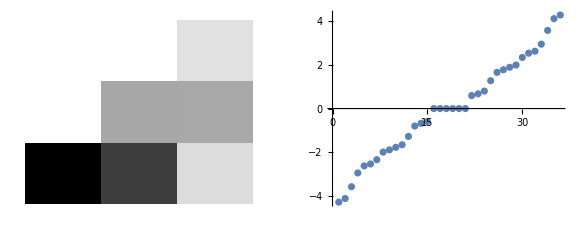

```mathematica
Hsubst=HfullMat/.solparam[[1]]/.solparamx[[1]]/.solparamy[[1]]/.{b10-> 0.2,b20-> 0.3,d10-> 0.1,b1x-> 0.4,b2x-> 0.26,t0x-> 0.14,b1y-> 0.31,b2y-> 0.06,t0y-> 0.16};
{evals,evec}=Eigensystem[Hsubst];
order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];evec=evecᵀ;
evecPlot=ArrayReshape[evec[[;;,2*Lx*Ly]],{Lx,Ly,4}];
new=Abs[#]^2&/@evecPlot;
new=new[[;;,;;,1]];
Print[evals[[2*Lx*Ly]]," ",evals[[2*Lx*Ly]]];
GraphicsRow[{ArrayPlot[new],ListPlot[evals]},ImageSize-> Large]
```

```mathematica
minEigen[Sy_,hfull_,lx_,ly_]:=Module[{evals,evec,order,evecPlot,new},
{evals,evec}=Eigensystem[hfull/.{t->1,bz->0, bx-> 1/2^(1/2), by-> 0, sx-> 0,sy-> Sy}];
order=Ordering[evals];
evals = evals[[order]];
Abs[evals[[2*lx*ly]]]]
```